Computational Journey of Quantum Mechanics | Amir H. Ebrahimnezhad | Advisor: Prf. Ebrahim | University of Tehran

# Advanced Topics in Computational Linear Algebra

## Overview

The following notebook serves as a complementary section for the previous one, where we’ve delved into linear algebra from symbolic computational point of view. In this notebook we would briefly introduce decompositions, matrix functions, and structured and sparse matrices. Later we work on extensions to infinite dimensional space, random matrix theory and Bohemian matrices, and lastly discuss multilinear algebra.

This notebook’s can be skipped since the topics might not be needed during other sections, but for the purpose of being a complete journey we shall discuss them.

## Matrix Decomposition

## Shur Decomposition

The Schur decomposition is a fundamental matrix factorization that transforms any square matrix into an upper triangular form through unitary similarity transformations. For any square matrix , the Shur decomposition states that:

where:

is a unitary matrix.

is an upper triangular matrix.

The diagonal elements of  are the eigenvalues of

The significance of this decomposition is in its universality, meaning that there always exists such decomposition for any square matrix, unlike diagonalization which requires a complete set of linearly independent eigenvectors. 

The Schur decomposition essentially provides a best attempt at diagonalization, leaving the matrix in an upper triangular form that reveals the eigen values on the diagonal.

```mathematica
(*Creating a sample matrix*)
A={{2.7,4.8,8.1},{-.6,1,0},{.1,0,.3}};
MatrixForm[A]

(*Computing the Schur decomposition*)
{U,T}=SchurDecomposition[A];

(*Display the factors*)
Print["Unitary matrix U:"]
MatrixForm[U]
Print["Upper triangular matrix T:"]
MatrixForm[T]

(*Verification*)
Print["Verification: A = U.T.U^*"]
MatrixForm[U.T.ConjugateTranspose[U]]
Print["Original matrix A:"]
MatrixForm[A]
Print["Difference:"]
MatrixForm[U.T.ConjugateTranspose[U]-A//Chop]
```

(2.7 | 4.8 | 8.1
-0.6 | 1 | 0
0.1 | 0 | 0.3)

Unitary matrix U:

(-0.969016 | 0.246437 | -0.0166355
0.243801 | 0.965103 | 0.0955848
-0.0396106 | -0.0885675 | 0.995282)

Upper triangular matrix T:

(1.91769 | -4.23924 | -8.19909
0.370608 | 1.91769 | 2.16431
0. | 0. | 0.164614)

Verification: A = U.T.U^*

(2.7 | 4.8 | 8.1
-0.6 | 1. | 1.38778×10^-16
0.1 | -4.51028×10^-17 | 0.3)

Original matrix A:

(2.7 | 4.8 | 8.1
-0.6 | 1 | 0
0.1 | 0 | 0.3)

Difference:

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

### Visualization

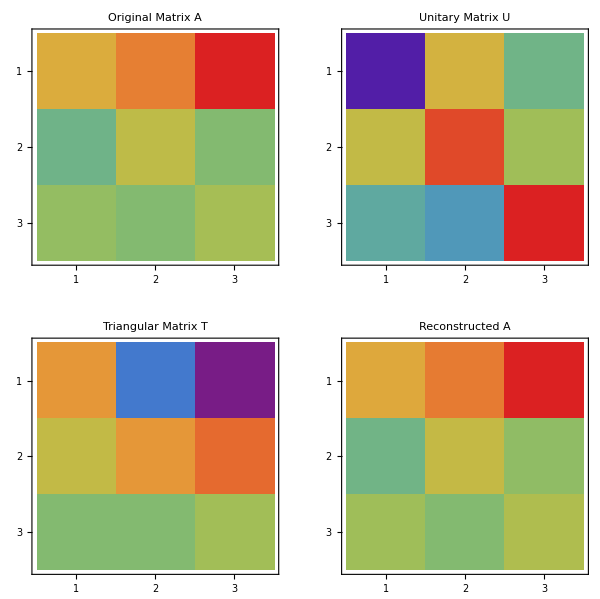

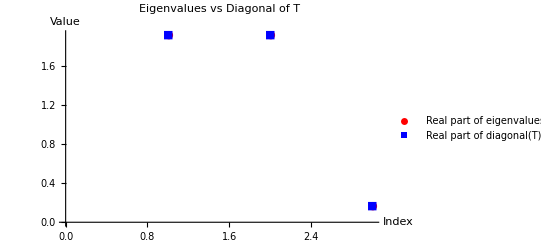

```mathematica
(*Visualization of the Schur decomposition*)
GraphicsGrid[{{MatrixPlot[A,ColorFunction->"Rainbow",PlotLabel->"Original Matrix A"],MatrixPlot[U,ColorFunction->"Rainbow",PlotLabel->"Unitary Matrix U"]},{MatrixPlot[T,ColorFunction->"Rainbow",PlotLabel->"Triangular Matrix T"],MatrixPlot[U.T.ConjugateTranspose[U],ColorFunction->"Rainbow",PlotLabel->"Reconstructed A"]}},ImageSize->600]

(*Visualizing the eigenvalues*)
eigenvalues=Eigenvalues[A];
diagonalT=Diagonal[T];

ListPlot[{Re[eigenvalues],Re[diagonalT]},PlotStyle->{Red,Blue},PlotLegends->{"Real part of eigenvalues","Real part of diagonal(T)"},PlotLabel->"Eigenvalues vs Diagonal of T",AxesLabel->{"Index","Value"},PlotMarkers->{"●","■"}]
```

## Jordan Canonical Form

The Jordan Canonical Form (JCF) represents one of the most important normal forms for matrices. Unlike the Shur form, the Jordan form is block diagonal, where each block (called a Jordan block) corresponds to an eigenvalue.

For any square matrix , the Jordan decomposition states that:

where

is an invertible matrix whose columns are generalized eigenvectors.

is the Jordan form, a block diagonal matrix where each block is a Jordan block.

Each Jordan block  has the form:

The Jordan form reveals the complete structure of a matrix in terms of its eigenvalues and generalized eigenvectors. It distinguishes between algebraic multiplicity (how many times an eigenvalue appears) and geometric multiplicity (the dimension of the eigenspace).

A diagonalizable matrix has a Jordan form with only  blocks (all eigenvalues appear on the diagonal with no  on the superdiagonal.

For non-diagonalizable matrices, the Jordan blocks of size greater than  indicate the deficiency in eigenvalues.

```mathematica
(*Creating a matrix with repeated eigenvalues-not diagonalizable*)
A={{2,1,3},{0,2,1},{0,2,2}};
MatrixForm[A]

(*Computing the Jordan decomposition*)
{P,J}=JordanDecomposition[A];

(*Display the factors*)
Print["Transformation matrix P:"]
MatrixForm[P]
Print["Jordan canonical form J:"]
MatrixForm[J]

(*Verification*)
Print["Verification: A = P.J.P^(-1)"]
MatrixForm[P.J.Inverse[P]]
Print["Original matrix A:"]
MatrixForm[A]
Print["Difference:"]
MatrixForm[P.J.Inverse[P]-A//Chop]

(*Examining the eigenvalues*)
eigenvalues=Eigenvalues[A];
Print["Eigenvalues of A:"]
eigenvalues
Print["Algebraic multiplicity of eigenvalue 2: ",Count[eigenvalues,2]]

(*Calculating the eigenvectors to show deficiency*)
eigenvectors=Eigenvectors[A];
Print["Eigenvectors of A:"]
eigenvectors
Print["Geometric multiplicity of eigenvalue 2: ",Length[eigenvectors]]
```

(2 | 1 | 3
0 | 2 | 1
0 | 2 | 2)

Transformation matrix P:

(1 | 1/2 (1-3 √2) | 1/2 (1+3 √2)
0 | -1/(√2) | 1/(√2)
0 | 1 | 1)

Jordan canonical form J:

(2 | 0 | 0
0 | 2-√2 | 0
0 | 0 | 2+√2)

Verification: A = P.J.P^(-1)

(2 | -6-((1-3 √2) (2-√2))/(2 √2)+((2+√2) (1+3 √2))/(2 √2) | -1+1/4 (1-3 √2) (2-√2)+1/4 (2+√2) (1+3 √2)
0 | 1/2 (2-√2)+1/2 (2+√2) | -(2-√2)/(2 √2)+(2+√2)/(2 √2)
0 | -(2-√2)/(√2)+(2+√2)/(√2) | 1/2 (2-√2)+1/2 (2+√2))

Original matrix A:

(2 | 1 | 3
0 | 2 | 1
0 | 2 | 2)

Difference:

(0 | -7-((1-3 √2) (2-√2))/(2 √2)+((2+√2) (1+3 √2))/(2 √2) | -4+1/4 (1-3 √2) (2-√2)+1/4 (2+√2) (1+3 √2)
0 | -2+1/2 (2-√2)+1/2 (2+√2) | -1-(2-√2)/(2 √2)+(2+√2)/(2 √2)
0 | -2-(2-√2)/(√2)+(2+√2)/(√2) | -2+1/2 (2-√2)+1/2 (2+√2))

Eigenvalues of A:

{2+√2,2,2-√2}

Algebraic multiplicity of eigenvalue 2: 1

Eigenvectors of A:

{{1/2 (1+3 √2),1/(√2),1},{1,0,0},{1/2 (1-3 √2),-1/(√2),1}}

Geometric multiplicity of eigenvalue 2: 3

### Visualization

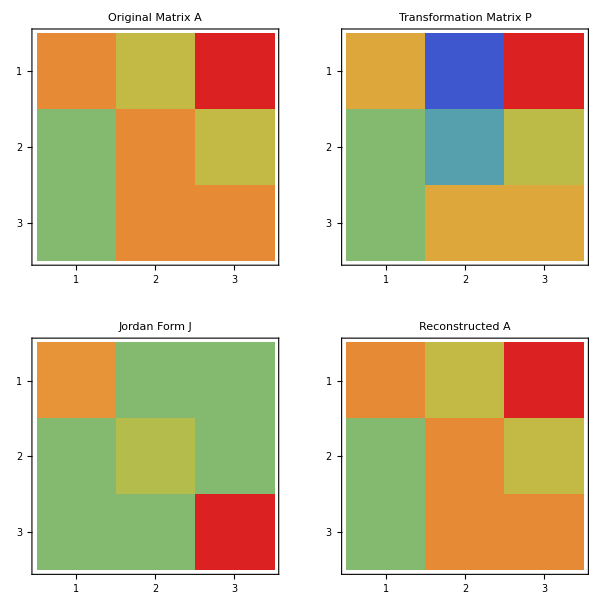

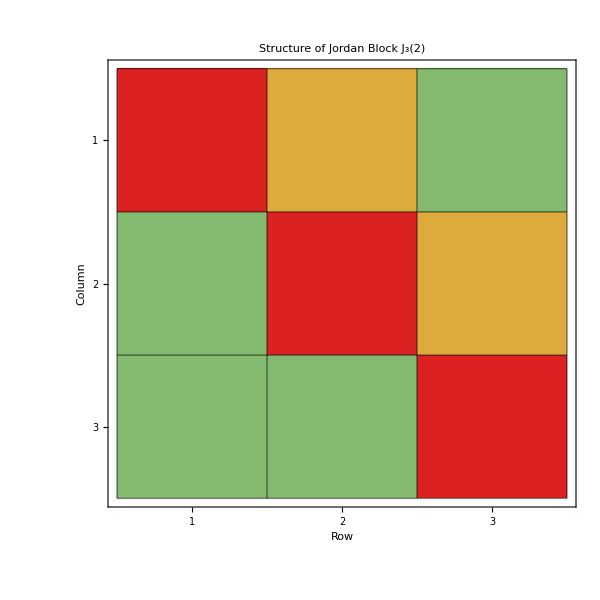

```mathematica
(*Visualization of the Jordan decomposition*)
GraphicsGrid[{{MatrixPlot[A,ColorFunction->"Rainbow",PlotLabel->"Original Matrix A"],MatrixPlot[P,ColorFunction->"Rainbow",PlotLabel->"Transformation Matrix P"]},{MatrixPlot[J,ColorFunction->"Rainbow",PlotLabel->"Jordan Form J"],MatrixPlot[P.J.Inverse[P],ColorFunction->"Rainbow",PlotLabel->"Reconstructed A"]}},ImageSize->600]

(*Visualizing Jordan block structure*)
Block[{size=3,λ=2},jordanBlock=SparseArray[{{i_,i_}->λ,{i_,j_}/;j==i+1->1},{size,size}];
MatrixPlot[jordanBlock,ColorFunction->"Rainbow",PlotLabel->"Structure of Jordan Block J₃(2)",Mesh->All,MeshStyle->Directive[Black,Opacity[0.5]],FrameLabel->{{"Row",None},{"Column",None}}]]
```

## Polar Decomposition

The Polar decomposition is analogous to expressing a complex number in polar form. For matrices, any square matrix  can be decomposed as:


where:

is a unitary matrix.

is a positive semidefinite Hermitian matrix.

For real matrices,  is orthogonal and  is symmetric positive semidefinite. The decomposition is unique if  is invertible, in which case  is positive definite. 

The polar decomposition has a clear geometric interpretation:  represents a scaling/stretching along its eigenvector directions, while  represents a rotation. This connection to physical transformations makes the polar decomposition particularly useful in applications like computer graphics, continuum mechanics and quantum physics.

The factors can be computed through the singular value decomposition (SVD) which we’ve dealt with in the previous notebook.
Given  then  and .

```mathematica
PolarDecomposition[A_]:=Module[{U, P, W, V, Sigma},
{W,Sigma,V}=SingularValueDecomposition[A];
U=W.ConjugateTranspose[V];
P=V.DiagonalMatrix[Diagonal[Sigma]].ConjugateTranspose[V];
{U//FullSimplify,P//FullSimplify}
]
(*Create a sample matrix*)
A={{3,1},{0,4}};
MatrixForm[A]

(*Compute the polar decomposition*)
{U,P}=PolarDecomposition[A];

(*Display the factors*)
Print["Unitary/Orthogonal factor U:"]
MatrixForm[U]
Print["Positive semidefinite factor P:"]
MatrixForm[P]

(*Verification*)
Print["Verification: A = U.P"]
U.P==A
Print["Difference:"]
MatrixForm[U.P-A//Chop]

(*Verify properties*)
Print["Is U orthogonal? ",Chop[Transpose[U].U-IdentityMatrix[2]]==ConstantArray[0,{2,2}]]
Print["Is P symmetric? ",Chop[P-Transpose[P]]==ConstantArray[0,{2,2}]]
Print["Is P positive semidefinite? ",And@@(#>=0&/@Eigenvalues[P])]
```

(3 | 1
0 | 4)

Unitary/Orthogonal factor U:

(7/(5 √2) | 1/(5 √2)
-1/(5 √2) | 7/(5 √2))

Positive semidefinite factor P:

(21/(5 √2) | 3/(5 √2)
3/(5 √2) | 29/(5 √2))

Verification: A = U.P

True

Difference:

(0 | 0
0 | 0)

Is U orthogonal? True

Is P symmetric? True

Is P positive semidefinite? True

### Visualization

-Graphics-

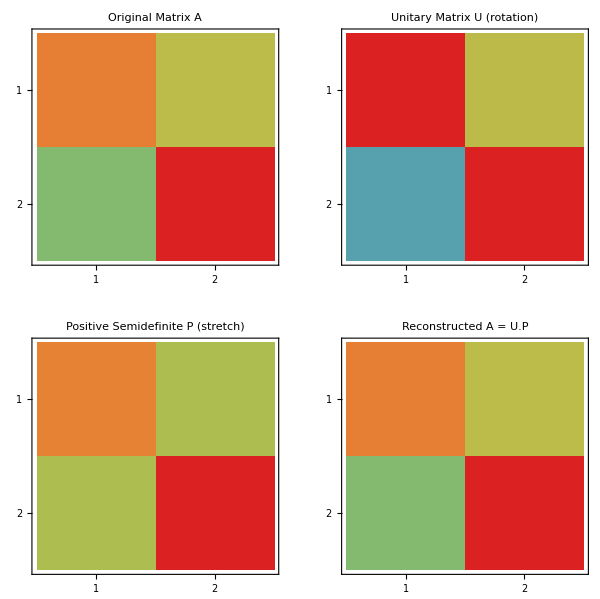

```mathematica
(*Visualization of polar decomposition's geometric interpretation*)(*First,we'll create a unit circle and transform it with A,U,and P*)
unitCircle=Table[{Cos[θ],Sin[θ]},{θ,0,2π,π/20}];
circleTransformedByA=Map[A.#&,unitCircle];
circleTransformedByU=Map[U.#&,unitCircle];
circleTransformedByP=Map[P.#&,unitCircle];

(*Plotting the transformations*)
Graphics[{{Thickness[0.005],Gray,Line[unitCircle]},(*Original circle*){Thickness[0.005],Red,Line[circleTransformedByA]},(*Transformed by A*){Thickness[0.005],Blue,Line[circleTransformedByU]},(*Rotated by U*){Thickness[0.005],Green,Line[circleTransformedByP]},(*Stretched by P*){Black,Arrow[{{0,0},{1,0}}]},(*x-axis*){Black,Arrow[{{0,0},{0,1}}]}  (*y-axis*)},PlotRange->{{-5,5},{-5,5}},PlotLabel->"Geometric Interpretation of Polar Decomposition",Epilog->{Text["Original",{1.2,0.2}],Text["A",{Sequence@@circleTransformedByA[[10]]}],Text["U (rotation)",{Sequence@@circleTransformedByU[[10]]}],Text["P (stretch)",{Sequence@@circleTransformedByP[[10]]}]},Axes->True,AxesLabel->{"x","y"},AspectRatio->1,ImageSize->500]

(*Matrix heat maps*)
GraphicsGrid[{{MatrixPlot[A,ColorFunction->"Rainbow",PlotLabel->"Original Matrix A"],MatrixPlot[U,ColorFunction->"Rainbow",PlotLabel->"Unitary Matrix U (rotation)"]},{MatrixPlot[P,ColorFunction->"Rainbow",PlotLabel->"Positive Semidefinite P (stretch)"],MatrixPlot[U.P,ColorFunction->"Rainbow",PlotLabel->"Reconstructed A = U.P"]}},ImageSize->600]
```

## Generalized Inverse (Moore-Penrose Inverse)

The Moore-Penrose inverse (or pseudoinverse) extends the concept of matrix inversion to non-square and singular matrices. For any matrix , the Moore-Penrose inverse  is the unique matrix satisfying all four Moore-Penrose conditions:

, and  (reflexivity).

, and  (, and  are Hermitian)

The Moore-Penrose inverse has numerous applications:

Least squares solutions: For an overdetermined system  gives the minimum norm least squares solution.

Rank determination: the rank of  equals the rank of .

Matrix decomposition: It’s closely related to the SVD.

Low-rank approximations: Used in principal component analysis and image compression.

For a matrix with full column rank, the pseudoinverse simplifies to , which is the left inverse. And for a matrix with full row rank. the pseudoinverse simplifies to  which is the right inverse. The pseudoinverse can be computed using the Singular Value Decomposition (SVD);

Given , then  where  is formed by taking the reciprocal of each non-zero singular value and transposing the resulting matrix.

```mathematica
(*Create a non-square matrix*)
A={{1,2,3},{4,5,6}};
MatrixForm[A]

(*Compute the Moore-Penrose inverse*)
Aplus=PseudoInverse[A];
Print["Moore-Penrose inverse:"]
MatrixForm[Aplus]

(*Verify the four Moore-Penrose conditions*)
Print["Checking Moore-Penrose conditions:"]
Print["1. A·A⁺·A = A? ",Chop[A.Aplus.A-A]==ConstantArray[0,Dimensions[A]]]
Print["2. A⁺·A·A⁺ = A⁺? ",Chop[Aplus.A.Aplus-Aplus]==ConstantArray[0,Dimensions[Aplus]]]
Print["3. (A·A⁺)* = A·A⁺? ",Chop[ConjugateTranspose[A.Aplus]-A.Aplus]==ConstantArray[0,{2,2}]]
Print["4. (A⁺·A)* = A⁺·A? ",Chop[ConjugateTranspose[Aplus.A]-Aplus.A]==ConstantArray[0,{3,3}]]

(*Compute via SVD*)
{U,Σ,V}=SingularValueDecomposition[A];
(*Create Σ⁺ by inverting non-zero singular values and transposing*)
ΣPlus=SparseArray[{i_,i_}/;Σ[[i,i]]!=0->1/Σ[[i,i]],Dimensions[Transpose[Σ]]];
AplusViaSVD=V.ΣPlus.ConjugateTranspose[U];
Print["Pseudoinverse via SVD:"]
MatrixForm[AplusViaSVD]
Print["Difference with direct computation:"]
MatrixForm[Aplus-AplusViaSVD//Chop]

(*Solve an overdetermined system using pseudoinverse*)
b={10,28};
Print["Solving overdetermined system Ax = b:"]
x=Aplus.b;
Print["Least squares solution x:"]
x
Print["Verification: Ax ≈ b? "]
A.x
Print["Residual norm ||Ax - b||: ",Norm[A.x-b]]
```

(1 | 2 | 3
4 | 5 | 6)

Moore-Penrose inverse:

(-17/18 | 4/9
-1/9 | 1/9
13/18 | -2/9)

Checking Moore-Penrose conditions:

1. A·A⁺·A = A? True

2. A⁺·A·A⁺ = A⁺? True

3. (A·A⁺)* = A·A⁺? True

4. (A⁺·A)* = A⁺·A? True

Part::partw: Part 30 of {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}} does not exist.

Pseudoinverse via SVD:

(((-63-√8065) (4+1/64 (-63-√8065)))/(64 √((1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧)+((-63+√8065) (4+1/64 (-63+√8065)))/(64 √((1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧) | (4+1/64 (-63-√8065))/(√((1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧)+(4+1/64 (-63+√8065))/(√((1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧)
((-63-√8065) (5+1/32 (-63-√8065)))/(64 √((1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧)+((-63+√8065) (5+1/32 (-63+√8065)))/(64 √((1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧) | (5+1/32 (-63-√8065))/(√((1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧)+(5+1/32 (-63+√8065))/(√((1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧)
((-63-√8065) (6+3/64 (-63-√8065)))/(64 √((1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧)+((-63+√8065) (6+3/64 (-63+√8065)))/(64 √((1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧) | (6+3/64 (-63-√8065))/(√((1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧)+(6+3/64 (-63+√8065))/(√((1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧))

Difference with direct computation:

(-17/18-((-63-√8065) (4+1/64 (-63-√8065)))/(64 √((1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧)-((-63+√8065) (4+1/64 (-63+√8065)))/(64 √((1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧) | 4/9-(4+1/64 (-63-√8065))/(√((1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧)-(4+1/64 (-63+√8065))/(√((1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧)
-1/9-((-63-√8065) (5+1/32 (-63-√8065)))/(64 √((1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧)-((-63+√8065) (5+1/32 (-63+√8065)))/(64 √((1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧) | 1/9-(5+1/32 (-63-√8065))/(√((1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧)-(5+1/32 (-63+√8065))/(√((1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧)
13/18-((-63-√8065) (6+3/64 (-63-√8065)))/(64 √((1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧)-((-63+√8065) (6+3/64 (-63+√8065)))/(64 √((1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧) | -2/9-(6+3/64 (-63-√8065))/(√((1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧)-(6+3/64 (-63+√8065))/(√((1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2)) {{√(1/2 (91+√8065)),0,0},{0,√(1/2 (91-√8065)),0}}⟦30,30⟧))

Solving overdetermined system Ax = b:

Least squares solution x:

{3,2,1}

Verification: Ax ≈ b?

{10,28}

Residual norm ||Ax - b||: 0

### Visualization

-Graphics3D-

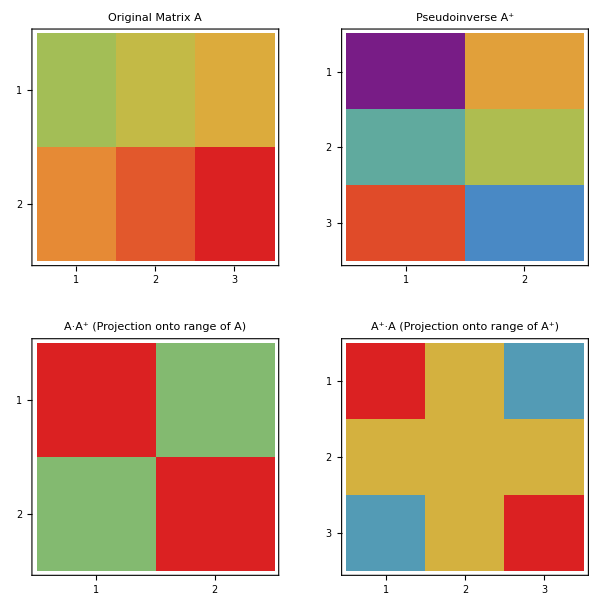

```mathematica
(*Visualize the action of a matrix and its pseudoinverse*)(*Let's create a simple example in 2D to 3D and back*)
A2={{1,0},{0,2},{1,1}};  (*3×2 matrix mapping R.b2->R.b3*)
A2plus=PseudoInverse[A2];     (*2×3 pseudoinverse mapping R.b3->R.b2*)

(*Create points in R.b2*)
points2D=Table[{Cos[t],Sin[t]},{t,0,2π,π/8}];

(*Map to R.b3*)
points3D=Map[A2.#&,points2D];

(*Map back with pseudoinverse*)
pointsRecovered=Map[A2plus.#&,points3D];

(*Visualize*)
Graphics3D[{{Red,PointSize[0.02],Point[Map[Append[#,0]&,points2D]]},(*Original in xy-plane*){Blue,PointSize[0.02],Point[points3D]},(*Mapped to 3D*){Green,PointSize[0.02],Point[Map[Append[#,0]&,pointsRecovered]]},(*Recovered in xy-plane*){Opacity[0.3],Gray,InfinitePlane[{{0,0,0},{1,0,0},{0,1,0}}]} (*xy-plane*)},PlotLabel->"Action of A and A⁺",Boxed->True,Axes->True,AxesLabel->{"x","y","z"},ViewPoint->{1.3,-2.4,2.0},Background->White,ImageSize->500]

(*Matrix heat maps*)
GraphicsGrid[{{MatrixPlot[A,ColorFunction->"Rainbow",PlotLabel->"Original Matrix A"],MatrixPlot[Aplus,ColorFunction->"Rainbow",PlotLabel->"Pseudoinverse A⁺"]},{MatrixPlot[A.Aplus,ColorFunction->"Rainbow",PlotLabel->"A·A⁺ (Projection onto range of A)"],MatrixPlot[Aplus.A,ColorFunction->"Rainbow",PlotLabel->"A⁺·A (Projection onto range of A⁺)"]}},ImageSize->600]
```

## Matrix Functions

## Definition

Matrix functions extend scalar functions to matrices, allowing us to compute expressions like , or  for matrices. These functions are defined for any square matrix and have important applications in differential equations, dynamical systems, quantum mechanics, and many other fields. The most general approach to defining matrix functions uses the Jordan canonical form. For a matrix  with Jordan decomposition , we define:
.

Since  is block diagonal, computing  reduces to computing the function on each Jordan block. For a Jordan block , the function is applied as:

-Graphics- (Sorry Mathematica had problem rendering it)

For diagonalizable matrices, where  with D diagonal, the formula simplifies to:



where  is the diagonal matrix with entries .

## Matrix Exponential

The matrix exponential is one of the most important matrix functions, with applications in solving systems of differential equations, continuous-time Markov chains, and Lie group theory. For a square matrix A, the matrix exponential is defined using the power series:

Key properties of the matrix exponential include:

=  if and only if  (matrices commute)

If  is diagonalizable as A, then  where  is a diagonal matrix

For any square matrix,

is always invertible with

The matrix exponential is especially important for solving systems of first-order linear differential equations:
; whose solution is .

```mathematica
(* Create a simple 2×2 matrix *)
A = {{0, 1}, {-1, 0}};
Print["Matrix A:"]
MatrixForm[A]

(* Compute the matrix exponential *)
expA = MatrixExp[A];
Print["Matrix exponential e^A:"]
MatrixForm[expA]

(* Compute using power series approximation (for demonstration) *)
powerSeriesExp[mat_, terms_] := 
  Sum[MatrixPower[mat, k]/Factorial[k], {k, 0, terms}];
  
expA_series = powerSeriesExp[A, 10];
Print["e^A via power series (10 terms):"]
MatrixForm[expA_series]
Print["Difference with direct computation:"]
MatrixForm[expA - expA_series // Chop]

(* For this particular matrix, e^A represents a rotation *)
(* Let's verify by applying it to some vectors *)
v = {1, 0};
expA.v // N
(* This should be approximately {0, 1}, a 90° rotation *)

(* Solving a differential equation system *)
Print["Solving differential equation x'(t) = Ax:"]
Print["Initial condition x(0) = {1, 0}"]
Print["Solution at t = π/2:"]
MatrixExp[A * (Pi/2)].{1, 0} // N
(* Should be approximately {0, 1}, a 90° rotation *)

(* Verify properties *)
Print["Properties of matrix exponential:"]
Print["det(e^A) = ", Det[expA] // N]
Print["e^tr(A) = ", Exp[Tr[A]] // N]
Print["(e^A)^(-1) = e^(-A)? ", 
  Norm[Inverse[expA] - MatrixExp[-A]] < 10^-10]
```

Matrix A:

(0 | 1
-1 | 0)

Matrix exponential e^A:

(Cos[1] | Sin[1]
-Sin[1] | Cos[1])

e^A via power series (10 terms):

expA_series

Difference with direct computation:

(Cos[1]-expA_series | -expA_series+Sin[1]
-expA_series-Sin[1] | Cos[1]-expA_series)

{0.540302,-0.841471}

Solving differential equation x'(t) = Ax:

Initial condition x(0) = {1, 0}

Solution at t = π/2:

{0.,-1.}

Properties of matrix exponential:

det(e^A) = 1.

e^tr(A) = 1.

(e^A)^(-1) = e^(-A)? True

### Visualization

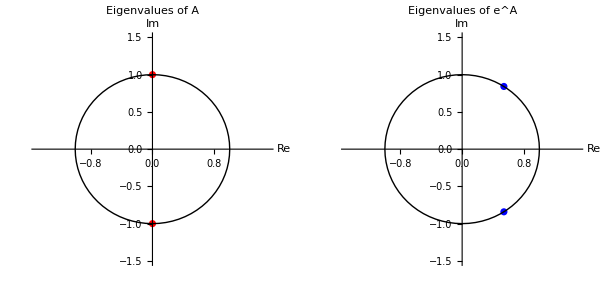

```mathematica
(* Visualize action of matrix exponential for different values of t *)
tValues = Range[0, 2π,0.1];
unitCircle = Table[{Cos[θ], Sin[θ]}, {θ, 0, 2π, π/20}];

(* Create frames for animation *)
frames = Table[
  Graphics[{
    {Thickness[0.005], LightGray, Line[unitCircle]}, (* Unit circle *)
    {Thickness[0.002], Dashed, Gray, 
     Line[{{0, 0}, {Cos[t], Sin[t]}}]}, (* Radius at angle t *)
    {Red, Arrow[{{0, 0}, {1, 0}}]}, (* Initial vector *)
    {Blue, Arrow[{{0, 0}, MatrixExp[A*t].{1, 0}}]}, (* Rotated vector *)
    {Black, Arrow[{{0, 0}, {1, 0}}]}, (* x-axis *)
    {Black, Arrow[{{0, 0}, {0, 1}}]}  (* y-axis *)
  },
  PlotRange -> {{-1.2, 1.2}, {-1.2, 1.2}},
  PlotLabel -> StringForm["e^(At) for t = ``", NumberForm[t, {3, 2}]],
  Axes -> True,
  AxesLabel -> {"x", "y"},
  AspectRatio -> 1,
  ImageSize -> 400], 
  {t, tValues}];

(* Display animation *)
ListAnimate[frames]

(* Visualize eigenvalues of A and e^A *)
eigenA = Eigenvalues[A];
eigenExpA = Eigenvalues[expA];

GraphicsGrid[{
  {ListPlot[ReIm[eigenA], PlotLabel -> "Eigenvalues of A", 
    AxesLabel -> {"Re", "Im"}, PlotStyle -> Red, 
    PlotRange -> {{-1.5, 1.5}, {-1.5, 1.5}}, AspectRatio -> 1,
    Epilog -> {Circle[{0, 0}, 1, {0, 2π}]}],
   ListPlot[ReIm[eigenExpA], PlotLabel -> "Eigenvalues of e^A", 
    AxesLabel -> {"Re", "Im"}, PlotStyle -> Blue, 
    PlotRange -> {{-1.5, 1.5}, {-1.5, 1.5}}, AspectRatio -> 1,
    Epilog -> {Circle[{0, 0}, 1, {0, 2π}]}]}
}, ImageSize -> 600]
```

## Logarithms and Matrix Sparse Roots

The matrix logarithm is the inverse of the matrix exponential . For a nonsingular matrix , the principal matrix logarithm  is the unique matrix  such that  and the eigenvalues of  lie within the strip  . Similarly, the principal square root of a matrix , denoted  or , is the unique matrix  such that  and the eigenvalues of  have positive real parts (when possible) . Both functions are well - defined for matrices with no eigenvalues on the negative real axis (for the logarithm) or zero (for the square root).

For a diagonalizable matrix :

where  applies the scalar logarithm to diagonal entries.

where  applies the scalar square root to diagonal entries

For non-diagonalizable matrices, the computation is more involved and requires the Jordan canonical form. Applications include solving matrix equations, computing fractional powers of matrices, and stability analysis of dynamical systems.

```mathematica
(* Create a positive definite matrix *)
A = {{4, 1}, {1, 3}};
Print["Matrix A:"]
MatrixForm[A]

(* Compute the matrix logarithm *)
logA = MatrixLog[A];
Print["Matrix logarithm log(A):"]
MatrixForm[logA]

(* Verify e^(log(A)) = A *)
Print["Verification: e^(log(A)) = A?"]
MatrixForm[MatrixExp[logA]]
Print["Difference:"]
MatrixForm[MatrixExp[logA] - A // Chop]

(* Compute the matrix square root *)
sqrtA = MatrixPower[A, 1/2];
Print["Matrix square root A^(1/2):"]
MatrixForm[sqrtA]

(* Verify (A^(1/2))^2 = A *)
Print["Verification: (A^(1/2))^2 = A?"]
MatrixForm[sqrtA.sqrtA]
Print["Difference:"]
MatrixForm[sqrtA.sqrtA - A // Chop]

(* Computing other matrix powers *)
Print["Computing A^(3/4):"]
MatrixForm[MatrixPower[A, 3/4]]

(* Connection between logarithm and square root *)
Print["log(A) vs 2*log(A^(1/2)):"]
Print["Difference:"]
MatrixForm[logA - 2*MatrixLog[sqrtA] // Chop]
```

Matrix A:

(4 | 1
1 | 3)

Matrix logarithm log(A):

(-((1-√5) Log[1/2 (7-√5)])/(2 √5)+((1+√5) Log[1/2 (7+√5)])/(2 √5) | -((-1-√5) (1-√5) Log[1/2 (7-√5)])/(4 √5)-((1-√5) (1+√5) Log[1/2 (7+√5)])/(4 √5)
-Log[1/2 (7-√5)]/(√5)+Log[1/2 (7+√5)]/(√5) | -((-1-√5) Log[1/2 (7-√5)])/(2 √5)-((1-√5) Log[1/2 (7+√5)])/(2 √5))

Verification: e^(log(A)) = A?

(((7+√5) (Log[1/2 (7-√5)]+√5 Log[1/2 (7-√5)]-Log[1/2 (7+√5)]-√5 Log[1/2 (7+√5)]))/(4 √5 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)]))-((-7+√5) (-Log[1/2 (7-√5)]+√5 Log[1/2 (7-√5)]+Log[1/2 (7+√5)]-√5 Log[1/2 (7+√5)]))/(4 √5 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)])) | ((-7+√5) (-1+√5) (1+√5))/(8 √5)+((-1+√5) (1+√5) (7+√5))/(8 √5)
((-7+√5) (√5 Log[1/2 (7-√5)]-√5 Log[1/2 (7+√5)]))/(10 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)]))+((7+√5) (√5 Log[1/2 (7-√5)]-√5 Log[1/2 (7+√5)]))/(10 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)])) | -((-7+√5) (Log[1/2 (7-√5)]+√5 Log[1/2 (7-√5)]-Log[1/2 (7+√5)]-√5 Log[1/2 (7+√5)]))/(4 √5 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)]))+((7+√5) (-Log[1/2 (7-√5)]+√5 Log[1/2 (7-√5)]+Log[1/2 (7+√5)]-√5 Log[1/2 (7+√5)]))/(4 √5 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)])))

Difference:

(-4+((7+√5) (Log[1/2 (7-√5)]+√5 Log[1/2 (7-√5)]-Log[1/2 (7+√5)]-√5 Log[1/2 (7+√5)]))/(4 √5 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)]))-((-7+√5) (-Log[1/2 (7-√5)]+√5 Log[1/2 (7-√5)]+Log[1/2 (7+√5)]-√5 Log[1/2 (7+√5)]))/(4 √5 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)])) | -1+((-7+√5) (-1+√5) (1+√5))/(8 √5)+((-1+√5) (1+√5) (7+√5))/(8 √5)
-1+((-7+√5) (√5 Log[1/2 (7-√5)]-√5 Log[1/2 (7+√5)]))/(10 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)]))+((7+√5) (√5 Log[1/2 (7-√5)]-√5 Log[1/2 (7+√5)]))/(10 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)])) | -3-((-7+√5) (Log[1/2 (7-√5)]+√5 Log[1/2 (7-√5)]-Log[1/2 (7+√5)]-√5 Log[1/2 (7+√5)]))/(4 √5 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)]))+((7+√5) (-Log[1/2 (7-√5)]+√5 Log[1/2 (7-√5)]+Log[1/2 (7+√5)]-√5 Log[1/2 (7+√5)]))/(4 √5 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)])))

Matrix square root A^(1/2):

(1/2 √(1/10 (7-√5)) (-1+√5)+1/2 (1+√5) √(1/10 (7+√5)) | -1/4 √(1/10 (7-√5)) (-1+√5) (1+√5)+1/4 (-1+√5) (1+√5) √(1/10 (7+√5))
-√(1/10 (7-√5))+√(1/10 (7+√5)) | 1/2 √(1/10 (7-√5)) (1+√5)+1/2 (-1+√5) √(1/10 (7+√5)))

Verification: (A^(1/2))^2 = A?

((1/2 √(1/10 (7-√5)) (-1+√5)+1/2 (1+√5) √(1/10 (7+√5)))^2+(-√(1/10 (7-√5))+√(1/10 (7+√5))) (-1/4 √(1/10 (7-√5)) (-1+√5) (1+√5)+1/4 (-1+√5) (1+√5) √(1/10 (7+√5))) | (1/2 √(1/10 (7-√5)) (1+√5)+1/2 (-1+√5) √(1/10 (7+√5))) (-1/4 √(1/10 (7-√5)) (-1+√5) (1+√5)+1/4 (-1+√5) (1+√5) √(1/10 (7+√5)))+(1/2 √(1/10 (7-√5)) (-1+√5)+1/2 (1+√5) √(1/10 (7+√5))) (-1/4 √(1/10 (7-√5)) (-1+√5) (1+√5)+1/4 (-1+√5) (1+√5) √(1/10 (7+√5)))
(-√(1/10 (7-√5))+√(1/10 (7+√5))) (1/2 √(1/10 (7-√5)) (1+√5)+1/2 (-1+√5) √(1/10 (7+√5)))+(-√(1/10 (7-√5))+√(1/10 (7+√5))) (1/2 √(1/10 (7-√5)) (-1+√5)+1/2 (1+√5) √(1/10 (7+√5))) | (1/2 √(1/10 (7-√5)) (1+√5)+1/2 (-1+√5) √(1/10 (7+√5)))^2+(-√(1/10 (7-√5))+√(1/10 (7+√5))) (-1/4 √(1/10 (7-√5)) (-1+√5) (1+√5)+1/4 (-1+√5) (1+√5) √(1/10 (7+√5))))

Difference:

(-4+(1/2 √(1/10 (7-√5)) (-1+√5)+1/2 (1+√5) √(1/10 (7+√5)))^2+(-√(1/10 (7-√5))+√(1/10 (7+√5))) (-1/4 √(1/10 (7-√5)) (-1+√5) (1+√5)+1/4 (-1+√5) (1+√5) √(1/10 (7+√5))) | -1+(1/2 √(1/10 (7-√5)) (1+√5)+1/2 (-1+√5) √(1/10 (7+√5))) (-1/4 √(1/10 (7-√5)) (-1+√5) (1+√5)+1/4 (-1+√5) (1+√5) √(1/10 (7+√5)))+(1/2 √(1/10 (7-√5)) (-1+√5)+1/2 (1+√5) √(1/10 (7+√5))) (-1/4 √(1/10 (7-√5)) (-1+√5) (1+√5)+1/4 (-1+√5) (1+√5) √(1/10 (7+√5)))
-1+(-√(1/10 (7-√5))+√(1/10 (7+√5))) (1/2 √(1/10 (7-√5)) (1+√5)+1/2 (-1+√5) √(1/10 (7+√5)))+(-√(1/10 (7-√5))+√(1/10 (7+√5))) (1/2 √(1/10 (7-√5)) (-1+√5)+1/2 (1+√5) √(1/10 (7+√5))) | -3+(1/2 √(1/10 (7-√5)) (1+√5)+1/2 (-1+√5) √(1/10 (7+√5)))^2+(-√(1/10 (7-√5))+√(1/10 (7+√5))) (-1/4 √(1/10 (7-√5)) (-1+√5) (1+√5)+1/4 (-1+√5) (1+√5) √(1/10 (7+√5))))

Computing A^(3/4):

(((7-√5)^(3/4) (-1+√5))/(2 2^(3/4) √5)+((1+√5) (7+√5)^(3/4))/(2 2^(3/4) √5) | -((1/2 (7-√5))^(3/4) (-1+√5) (1+√5))/(4 √5)+((-1+√5) (1+√5) (1/2 (7+√5))^(3/4))/(4 √5)
-(7-√5)^(3/4)/(2^(3/4) √5)+(7+√5)^(3/4)/(2^(3/4) √5) | ((7-√5)^(3/4) (1+√5))/(2 2^(3/4) √5)+((-1+√5) (7+√5)^(3/4))/(2 2^(3/4) √5))

log(A) vs 2*log(A^(1/2)):

Difference:

(-((1-√5) Log[1/2 (7-√5)])/(2 √5)+((1+√5) Log[1/2 (7+√5)])/(2 √5)-2 (((√(10 (7-√5))-√(10 (7+√5))+10 √(7-2 √11)) Log[1/4 (√(14-2 √5)+√(2 (7+√5))-2 √(7-2 √11))])/(20 √(7-2 √11))-((√(10 (7-√5))-√(10 (7+√5))-10 √(7-2 √11)) Log[1/4 (√(14-2 √5)+√(2 (7+√5))+2 √(7-2 √11))])/(20 √(7-2 √11))) | -((-1-√5) (1-√5) Log[1/2 (7-√5)])/(4 √5)-((1-√5) (1+√5) Log[1/2 (7+√5)])/(4 √5)-2 (-((√(10 (7-√5))-√(10 (7+√5))-10 √(7-2 √11)) (√(10 (7-√5))-√(10 (7+√5))+10 √(7-2 √11)) Log[1/4 (√(14-2 √5)+√(2 (7+√5))-2 √(7-2 √11))])/(40 √(10 (7-2 √11)) (√(7-√5)-√(7+√5)))+((√(10 (7-√5))-√(10 (7+√5))-10 √(7-2 √11)) (√(10 (7-√5))-√(10 (7+√5))+10 √(7-2 √11)) Log[1/4 (√(14-2 √5)+√(2 (7+√5))+2 √(7-2 √11))])/(40 √(10 (7-2 √11)) (√(7-√5)-√(7+√5))))
-Log[1/2 (7-√5)]/(√5)+Log[1/2 (7+√5)]/(√5)-2 (((√(7-√5)-√(7+√5)) Log[1/4 (√(14-2 √5)+√(2 (7+√5))-2 √(7-2 √11))])/(√(10 (7-2 √11)))-((√(7-√5)-√(7+√5)) Log[1/4 (√(14-2 √5)+√(2 (7+√5))+2 √(7-2 √11))])/(√(10 (7-2 √11)))) | -((-1-√5) Log[1/2 (7-√5)])/(2 √5)-((1-√5) Log[1/2 (7+√5)])/(2 √5)-2 (-((√(10 (7-√5))-√(10 (7+√5))-10 √(7-2 √11)) Log[1/4 (√(14-2 √5)+√(2 (7+√5))-2 √(7-2 √11))])/(20 √(7-2 √11))+((√(10 (7-√5))-√(10 (7+√5))+10 √(7-2 √11)) Log[1/4 (√(14-2 √5)+√(2 (7+√5))+2 √(7-2 √11))])/(20 √(7-2 √11))))

### Visualization

-Graphics-

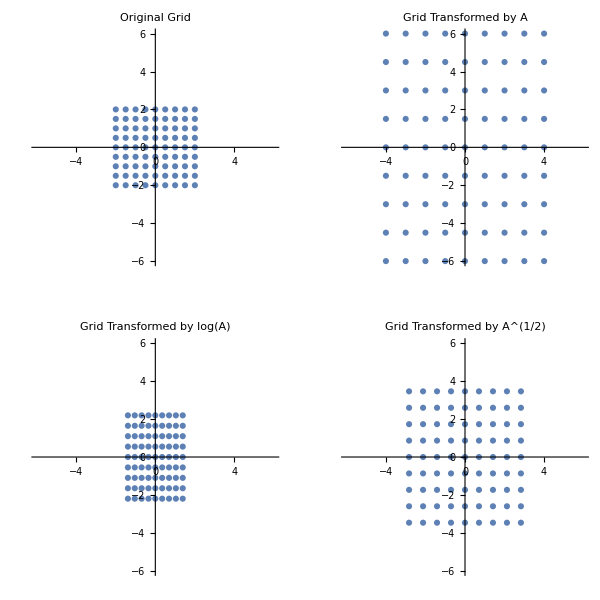

```mathematica
(* Visualize the spectral mapping between A, log(A), and sqrt(A) *)
eigenA = Eigenvalues[A];
eigenLogA = Eigenvalues[logA];
eigenSqrtA = Eigenvalues[sqrtA];

GraphicsGrid[{
  {ListPlot[eigenA, PlotLabel -> "Eigenvalues of A", 
    AxesLabel -> {"Re", "Im"}, PlotStyle -> Red],
   ListPlot[eigenLogA, PlotLabel -> "Eigenvalues of log(A)", 
    AxesLabel -> {"Re", "Im"}, PlotStyle -> Blue]},
  {ListPlot[eigenSqrtA, PlotLabel -> "Eigenvalues of A^(1/2)", 
    AxesLabel -> {"Re", "Im"}, PlotStyle -> Green],
   ListPlot[{eigenA, Map[#^(1/2) &, eigenA]}, 
    PlotLabel -> "λ vs λ^(1/2)", PlotStyle -> {Red, Green},
    AxesLabel -> {"Re", "Im"}, 
    PlotLegends -> {"λ(A)", "λ(A)^(1/2)"}]}
}, ImageSize -> 600]

(* Visualizing the action of matrix logarithm and square root *)
(* We'll use a simpler matrix for better visualization *)
B = {{2, 0}, {0, 3}};
logB = MatrixLog[B];
sqrtB = MatrixPower[B, 1/2];

(* Create a grid of points *)
grid = Flatten[Table[{x, y}, {x, -2, 2, 0.5}, {y, -2, 2, 0.5}], 1];

(* Transform grid with B, log(B), and sqrt(B) *)
gridB = Map[B.# &, grid];
gridLogB = Map[logB.# &, grid];
gridSqrtB = Map[sqrtB.# &, grid];

(* Plot transformations *)
GraphicsGrid[{
  {ListPlot[grid, PlotLabel -> "Original Grid", 
    AspectRatio -> 1, PlotRange -> {{-6, 6}, {-6, 6}}],
   ListPlot[gridB, PlotLabel -> "Grid Transformed by A", 
    AspectRatio -> 1, PlotRange -> {{-6, 6}, {-6, 6}}]},
  {ListPlot[gridLogB, PlotLabel -> "Grid Transformed by log(A)", 
    AspectRatio -> 1, PlotRange -> {{-6, 6}, {-6, 6}}],
   ListPlot[gridSqrtB, PlotLabel -> "Grid Transformed by A^(1/2)", 
    AspectRatio -> 1, PlotRange -> {{-6, 6}, {-6, 6}}]}
}, ImageSize -> 600]
```

## Functional Calculus For Matrices

The functional calculus provides a systematic framework for defining functions of matrices beyond basic operations like logarithms and square roots . It allows us to apply virtually any well - behaved function to a matrix. For any function f that is analytic on and inside a contour \Gamma enclosing all eigenvalues of A, we can define f(A) using the Cauchy integral formula:

.

This definition agrees with the power series definition when  can be represented as a power series. Another approach uses the spectral decomposition. For a diagonalizable matrix  with eigen-decomposition , where  are the spectral projectors, we define: .

This approach generalizes to the case where  is not diagonalizable using the Jordan canonical form. Practical methods for computing matrix functions include:

Diagonalization: If , then

Schur decomposition: If , then .

Padé approximation: Useful for functions like  and

Scaling and squaring: Especially efficient for computing

Polynomial approximation: Using Chebyshev or Taylor series

The functional calculus is used in solving differential equations, quantum mechanics, control theory, and network analysis.

```mathematica
(* Create a matrix *)
A = {{1, 2}, {3, 4}};
Print["Matrix A:"]
MatrixForm[A]

(* Define some matrix functions using MatrixFunction *)
sinA = MatrixFunction[Sin, A];
Print["sin(A):"]
MatrixForm[sinA]

cosA = MatrixFunction[Cos, A];
Print["cos(A):"]
MatrixForm[cosA]

(* Verify the identity sin^2(A) + cos^2(A) = I *)
Print["sin^2(A) + cos^2(A):"]
MatrixForm[sinA.sinA + cosA.cosA // Chop]

(* Using Diagonalization approach *)
{eigenvalues, P} = Eigensystem[A];
Diag = DiagonalMatrix[eigenvalues];
PInv = Inverse[Transpose[P]];

(* Computing sin(A) via diagonalization *)
sinD = DiagonalMatrix[Map[Sin, eigenvalues]];
sinA_diag = P.sinD.PInv;
Print["sin(A) via diagonalization:"]
MatrixForm[sinA_diag]
Print["Difference with direct computation:"]
MatrixForm[sinA - sinA_diag // Chop]

(* Define a more complex function *)
f[x_] := Exp[-x^2] * Sin[x];
fA = MatrixFunction[f, A];
Print["f(A) = e^(-A^2) * sin(A):"]
MatrixForm[fA]

(* Computing a matrix sign function *)
signA = MatrixFunction[Sign, A];
Print["sign(A):"]
MatrixForm[signA]

(* Verify sign(A)^2 = I *)
Print["sign(A)^2:"]
MatrixForm[signA.signA // Chop]
```

Matrix A:

(1 | 2
3 | 4)

sin(A):

(-((-3-√33) Sin[1/2 (5-√33)])/(2 √33)+((-3+√33) Sin[1/2 (5+√33)])/(2 √33) | -((-3-√33) (3-√33) Sin[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Sin[1/2 (5+√33)])/(12 √33)
-√(3/11) Sin[1/2 (5-√33)]+√(3/11) Sin[1/2 (5+√33)] | -((3-√33) Sin[1/2 (5-√33)])/(2 √33)-((-3-√33) Sin[1/2 (5+√33)])/(2 √33))

cos(A):

(-((-3-√33) Cos[1/2 (5-√33)])/(2 √33)+((-3+√33) Cos[1/2 (5+√33)])/(2 √33) | -((-3-√33) (3-√33) Cos[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Cos[1/2 (5+√33)])/(12 √33)
-√(3/11) Cos[1/2 (5-√33)]+√(3/11) Cos[1/2 (5+√33)] | -((3-√33) Cos[1/2 (5-√33)])/(2 √33)-((-3-√33) Cos[1/2 (5+√33)])/(2 √33))

sin^2(A) + cos^2(A):

((-((-3-√33) Cos[1/2 (5-√33)])/(2 √33)+((-3+√33) Cos[1/2 (5+√33)])/(2 √33))^2+(-√(3/11) Cos[1/2 (5-√33)]+√(3/11) Cos[1/2 (5+√33)]) (-((-3-√33) (3-√33) Cos[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Cos[1/2 (5+√33)])/(12 √33))+(-((-3-√33) Sin[1/2 (5-√33)])/(2 √33)+((-3+√33) Sin[1/2 (5+√33)])/(2 √33))^2+(-√(3/11) Sin[1/2 (5-√33)]+√(3/11) Sin[1/2 (5+√33)]) (-((-3-√33) (3-√33) Sin[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Sin[1/2 (5+√33)])/(12 √33)) | (-((3-√33) Cos[1/2 (5-√33)])/(2 √33)-((-3-√33) Cos[1/2 (5+√33)])/(2 √33)) (-((-3-√33) (3-√33) Cos[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Cos[1/2 (5+√33)])/(12 √33))+(-((-3-√33) Cos[1/2 (5-√33)])/(2 √33)+((-3+√33) Cos[1/2 (5+√33)])/(2 √33)) (-((-3-√33) (3-√33) Cos[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Cos[1/2 (5+√33)])/(12 √33))+(-((3-√33) Sin[1/2 (5-√33)])/(2 √33)-((-3-√33) Sin[1/2 (5+√33)])/(2 √33)) (-((-3-√33) (3-√33) Sin[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Sin[1/2 (5+√33)])/(12 √33))+(-((-3-√33) Sin[1/2 (5-√33)])/(2 √33)+((-3+√33) Sin[1/2 (5+√33)])/(2 √33)) (-((-3-√33) (3-√33) Sin[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Sin[1/2 (5+√33)])/(12 √33))
(-√(3/11) Cos[1/2 (5-√33)]+√(3/11) Cos[1/2 (5+√33)]) (-((3-√33) Cos[1/2 (5-√33)])/(2 √33)-((-3-√33) Cos[1/2 (5+√33)])/(2 √33))+(-√(3/11) Cos[1/2 (5-√33)]+√(3/11) Cos[1/2 (5+√33)]) (-((-3-√33) Cos[1/2 (5-√33)])/(2 √33)+((-3+√33) Cos[1/2 (5+√33)])/(2 √33))+(-√(3/11) Sin[1/2 (5-√33)]+√(3/11) Sin[1/2 (5+√33)]) (-((3-√33) Sin[1/2 (5-√33)])/(2 √33)-((-3-√33) Sin[1/2 (5+√33)])/(2 √33))+(-√(3/11) Sin[1/2 (5-√33)]+√(3/11) Sin[1/2 (5+√33)]) (-((-3-√33) Sin[1/2 (5-√33)])/(2 √33)+((-3+√33) Sin[1/2 (5+√33)])/(2 √33)) | (-((3-√33) Cos[1/2 (5-√33)])/(2 √33)-((-3-√33) Cos[1/2 (5+√33)])/(2 √33))^2+(-√(3/11) Cos[1/2 (5-√33)]+√(3/11) Cos[1/2 (5+√33)]) (-((-3-√33) (3-√33) Cos[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Cos[1/2 (5+√33)])/(12 √33))+(-((3-√33) Sin[1/2 (5-√33)])/(2 √33)-((-3-√33) Sin[1/2 (5+√33)])/(2 √33))^2+(-√(3/11) Sin[1/2 (5-√33)]+√(3/11) Sin[1/2 (5+√33)]) (-((-3-√33) (3-√33) Sin[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Sin[1/2 (5+√33)])/(12 √33)))

sin(A) via diagonalization:

sinA_diag

Difference with direct computation:

(-sinA_diag-((-3-√33) Sin[1/2 (5-√33)])/(2 √33)+((-3+√33) Sin[1/2 (5+√33)])/(2 √33) | -sinA_diag-((-3-√33) (3-√33) Sin[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Sin[1/2 (5+√33)])/(12 √33)
-sinA_diag-√(3/11) Sin[1/2 (5-√33)]+√(3/11) Sin[1/2 (5+√33)] | -sinA_diag-((3-√33) Sin[1/2 (5-√33)])/(2 √33)-((-3-√33) Sin[1/2 (5+√33)])/(2 √33))

f(A) = e^(-A^2) * sin(A):

(-((-3-√33) ⅇ^(-1/4 (5-√33)^2) Sin[1/2 (5-√33)])/(2 √33)+((-3+√33) ⅇ^(-1/4 (5+√33)^2) Sin[1/2 (5+√33)])/(2 √33) | -((-3-√33) (3-√33) ⅇ^(-1/4 (5-√33)^2) Sin[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) ⅇ^(-1/4 (5+√33)^2) Sin[1/2 (5+√33)])/(12 √33)
-√(3/11) ⅇ^(-1/4 (5-√33)^2) Sin[1/2 (5-√33)]+√(3/11) ⅇ^(-1/4 (5+√33)^2) Sin[1/2 (5+√33)] | -((3-√33) ⅇ^(-1/4 (5-√33)^2) Sin[1/2 (5-√33)])/(2 √33)-((-3-√33) ⅇ^(-1/4 (5+√33)^2) Sin[1/2 (5+√33)])/(2 √33))

sign(A):

((-3+√33)/(2 √33)-(3+√33)/(2 √33) | -((-3-√33) (-3+√33))/(12 √33)-((3-√33) (3+√33))/(12 √33)
2 √(3/11) | -(-3-√33)/(2 √33)+(3-√33)/(2 √33))

sign(A)^2:

(((-3+√33)/(2 √33)-(3+√33)/(2 √33))^2+2 √(3/11) (-((-3-√33) (-3+√33))/(12 √33)-((3-√33) (3+√33))/(12 √33)) | (-(-3-√33)/(2 √33)+(3-√33)/(2 √33)) (-((-3-√33) (-3+√33))/(12 √33)-((3-√33) (3+√33))/(12 √33))+((-3+√33)/(2 √33)-(3+√33)/(2 √33)) (-((-3-√33) (-3+√33))/(12 √33)-((3-√33) (3+√33))/(12 √33))
2 √(3/11) (-(-3-√33)/(2 √33)+(3-√33)/(2 √33))+2 √(3/11) ((-3+√33)/(2 √33)-(3+√33)/(2 √33)) | (-(-3-√33)/(2 √33)+(3-√33)/(2 √33))^2+2 √(3/11) (-((-3-√33) (-3+√33))/(12 √33)-((3-√33) (3+√33))/(12 √33)))

### Visualization

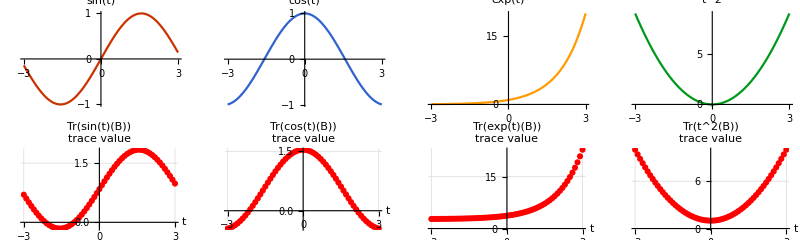

-Graphics3D-

```mathematica
(* Visualizing scalar functions vs matrix functions *)
tValues = Range[-3, 3, 0.1];
scalarFunctions = {
  Sin[#] &,
  Cos[#] &,
  Exp[#] &,
  #^2 &
};
functionNames = {"sin(t)", "cos(t)", "exp(t)", "t^2"};

(* Plot scalar functions *)
scalarPlots = Table[
  Plot[scalarFunctions[[i]][t], {t, -3, 3},
    PlotLabel -> functionNames[[i]],
    PlotStyle -> ColorData[112][i]],
  {i, 1, Length[scalarFunctions]}
];

(* Matrix B parameterized by t *)
matrixFunctionPlot[func_, name_] := Module[{B, fB, eigenvalues, trace},
  ListPlot[Table[
    B = {{1, 0}, {0, t}};  (* Diagonal matrix with eigenvalues 1 and t *)
    fB = MatrixFunction[func, B];
    eigenvalues = Eigenvalues[fB];
    trace = Tr[fB];
    {t, trace},
    {t, -3, 3, 0.1}],
    PlotLabel -> "Tr(" <> name <> "(B))",
    PlotStyle -> Red,
    AxesLabel -> {"t", "trace value"},
    GridLines -> Automatic
  ]
];

(* Generate matrix function plots *)
matrixPlots = Table[
  matrixFunctionPlot[scalarFunctions[[i]], functionNames[[i]]],
  {i, 1, Length[scalarFunctions]}
];

(* Display both types of plots *)
GraphicsGrid[{scalarPlots, matrixPlots}, ImageSize -> 800]

(* 3D visualization of matrix exponential for 2×2 matrices *)
(* We'll parameterize A = {{a, b}, {c, d}} and plot det(e^A) = e^tr(A) *)
plotPoints = Flatten[Table[
  {a, d, Exp[a + d]},
  {a, -2, 2, 0.2},
  {d, -2, 2, 0.2}
], 1];

ListPlot3D[plotPoints,
  PlotLabel -> "det(e^A) = e^tr(A) for A = {{a, b}, {c, d}}",
  AxesLabel -> {"a", "d", "det(e^A)"},
  ColorFunction -> "Rainbow",
  Mesh -> None,
  PlotRange -> All,
  ViewPoint -> {1.3, -2.4, 2.0},
  BoxRatios -> {1, 1, 1},
  ImageSize -> 500]
```

These matrix functions provide powerful tools for solving problems in differential equations, dynamical systems, quantum mechanics, and many other fields. The functional calculus framework unifies these operations and allows us to apply virtually any analytic function to matrices in a consistent and mathematically sound way.

## Structured & Sparse Matrices

## Special Structures

Structured matrices play a critical role in computational linear algebra due to their unique properties, which can be exploited to develop more efficient algorithms and storage schemes. In this section, we’ll explore three important classes of structured matrices: Toeplitz, Hankel, and Circulant matrices, all of which have distinctive patterns that appear in various applications.

### Toeplitz Matrices

A Toeplitz matrix is a matrix in which each descending diagonal from left to right contains the same element . For an  Toeplitz matrix , the entries satisfy :
   
   

This means that the  entry depends only on the difference between  and  . The general form of an  Toeplitz matrix is :

-Graphics-

Toeplitz matrices are completely determined by  values :  . Key properties of Toeplitz matrices include:

The sum of two Toeplitz matrices is Toeplitz

The product of two Toeplitz matrices is generally not Toeplitz

Toeplitz matrices are persymmetric (symmetric with respect to the anti-diagonal)

The transpose of a Toeplitz matrix is Toeplitz

Symmetric Toeplitz matrices have additional computational advantages

Toeplitz matrices appear in signal processing (for convolution operations), time series analysis, differential and integral equations, and image processing.

```mathematica
(* Example *)
c = {1, 2, 3, 4, 5}; (* First column *)
r = {1, 6, 7, 8, 9}; (* First row *)

T = ToeplitzMatrix[c, r];
Print["Toeplitz Matrix:"]
MatrixForm[T]

(* Verify the Toeplitz property *)
Print["Checking Toeplitz property:"]
allDiags = Table[Diagonal[T, k], {k, -(Length[c] - 1), Length[r] - 1}];
allDiagsEqual = And @@ Map[
  Apply[Equal, #] &,
  allDiags
];
Print["All elements along each diagonal are equal? ", allDiagsEqual]

(* Efficient storage representation *)
Print["Efficient representation (only 2n-1 values):"]
diagonalValues = Join[Reverse[r[[2 ;; All]]], c];
diagonalValues

(* Solving Toeplitz systems *)
(* Using the Levinson algorithm (built into Mathematica) *)
b = {10, 20, 30, 40, 50};
solution = LinearSolve[T, b];
Print["Solution to Tx = b:"]
solution
Print["Verification T.x = b:"]
T.solution

(* Defining a symmetric Toeplitz matrix *)
symC = {5, 4, 3, 2, 1};
symR = {5, 4, 3, 2, 1};
symT = ToeplitzMatrix[symC, symR];
Print["Symmetric Toeplitz Matrix:"]
MatrixForm[symT]
```

Toeplitz Matrix:

(1 | 6 | 7 | 8 | 9
2 | 1 | 6 | 7 | 8
3 | 2 | 1 | 6 | 7
4 | 3 | 2 | 1 | 6
5 | 4 | 3 | 2 | 1)

Checking Toeplitz property:

All elements along each diagonal are equal? True

Efficient representation (only 2n-1 values):

{9,8,7,6,1,2,3,4,5}

Solution to Tx = b:

{10,0,0,0,0}

Verification T.x = b:

{10,20,30,40,50}

Symmetric Toeplitz Matrix:

(5 | 4 | 3 | 2 | 1
4 | 5 | 4 | 3 | 2
3 | 4 | 5 | 4 | 3
2 | 3 | 4 | 5 | 4
1 | 2 | 3 | 4 | 5)

#### Visualization

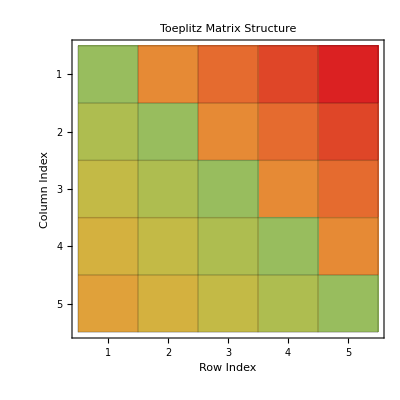

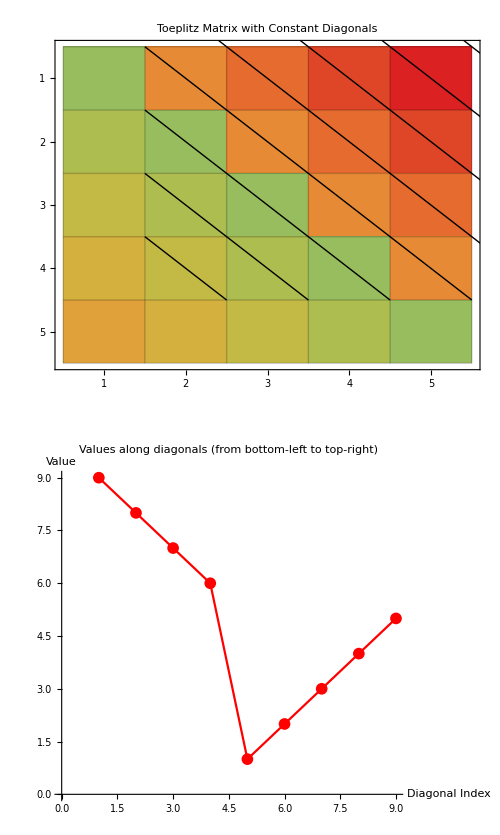

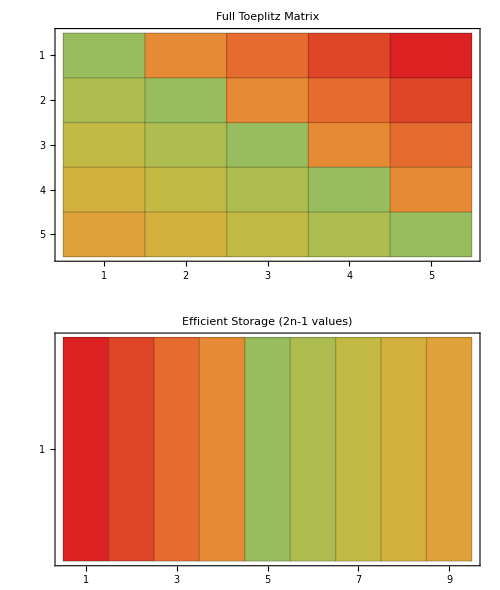

```mathematica
(* Visualize the structure of a Toeplitz matrix *)
MatrixPlot[T, 
  ColorFunction -> "Rainbow",
  PlotLabel -> "Toeplitz Matrix Structure",
  Mesh -> All,
  MeshStyle -> Opacity[0.2],
  FrameLabel -> {{"Row Index", None}, {"Column Index", None}}]

(* Visualize diagonals *)
GraphicsGrid[{
  {MatrixPlot[T, 
     ColorFunction -> "Rainbow",
     PlotLabel -> "Toeplitz Matrix with Constant Diagonals",
     Epilog -> Table[
       Line[{{1, i}, {i, 1}}], 
       {i, 1, Length[c] + Length[r] - 1}],
     Mesh -> All, 
     MeshStyle -> Opacity[0.2]]},
  {ListLinePlot[diagonalValues, 
     PlotLabel -> "Values along diagonals (from bottom-left to top-right)",
     AxesLabel -> {"Diagonal Index", "Value"},
     PlotStyle -> Red,
     PlotMarkers -> {"●", 12}]}
}, ImageSize -> 500]

(* Show the efficient storage *)
GraphicsGrid[{
  {MatrixPlot[T, 
     ColorFunction -> "Rainbow",
     PlotLabel -> "Full Toeplitz Matrix",
     Mesh -> All, 
     MeshStyle -> Opacity[0.2]]},
  {MatrixPlot[{diagonalValues}, 
     ColorFunction -> "Rainbow",
     PlotLabel -> "Efficient Storage (2n-1 values)",
     Mesh -> All, 
     MeshStyle -> Opacity[0.2]]}
}, ImageSize -> 500]
```

### Hankel Matrices

A Hankel matrix is a square matrix in which each ascending skew - diagonal from left to right contains the same element . For an  Hankel matrix , the entries satisfy :
   
   

This means that the  entry depends only on the sum of  and  . The general form of an n \times n Hankel matrix is :
   
-Graphics-

Hankel matrices are completely determined by  values :  . Key properties of Hankel matrices include :

The sum of two Hankel matrices is Hankel.

The product of two Hankel matrices is generally not Hankel.

Hankel matrices are symmetric with respect to the anti-diagonal (persymmetric).

The product of a Hankel matrix and a Toeplitz matrix can be computed efficiently

Hankel matrices appear in moment problems, approximation theory, control theory, and signal processing. They are often used in system identification and realization.

```mathematica
(* Example with first column and last row *)
c = {1, 2, 3, 4, 5}; (* First column *)
r = {5, 6, 7, 8, 9}; (* Last row *)

H = HankelMatrix[c, r];
Print["Hankel Matrix:"]
MatrixForm[H]

(* Alternative implementation directly using the property *)
HankelMatrixDirect[values_] := Table[
  values[[i + j - 1]],
  {i, 1, Ceiling[Length[values]/2]}, 
  {j, 1, Ceiling[Length[values]/2]}
];

values = {1, 2, 3, 4, 5, 6, 7, 8, 9};
H2 = HankelMatrixDirect[values];
Print["Hankel Matrix from sequential values:"]
MatrixForm[H2]

Print["Checking Hankel property:"];

(*get dimensions*)
{nRows,nCols}=Dimensions[H];

(*Group elements by (i+j)*)
antiDiagonals=Table[Select[Flatten[Table[{i,j,H[[i,j]]},{i,1,nRows},{j,1,nCols}],1],(#[[1]]+#[[2]]==k)&][[All,3]],{k,2,nRows+nCols}];

(*Check if each anti-diagonal has all equal elements*)
allAntiDiagsEqual=And@@Map[SameQ@@#&,antiDiagonals];

Print["All elements along each anti-diagonal are equal? ",allAntiDiagsEqual];


(* Relationship between Hankel and Toeplitz matrices *)
(* A Hankel matrix can be converted to a Toeplitz matrix by reversing each row *)
Print["Converting Hankel to Toeplitz by row reversal:"]
HankelToToeplitz = Map[Reverse, H];
MatrixForm[HankelToToeplitz]
Print["Is this a Toeplitz matrix? ", 
  And @@ Flatten[Table[HankelToToeplitz[[i, j]] == HankelToToeplitz[[i+1, j+1]], 
    {i, 1, Dimensions[HankelToToeplitz][[1]]-1}, 
    {j, 1, Dimensions[HankelToToeplitz][[2]]-1}]]]
```

Hankel Matrix:

(1 | 2 | 3 | 4 | 5
2 | 3 | 4 | 5 | 6
3 | 4 | 5 | 6 | 7
4 | 5 | 6 | 7 | 8
5 | 6 | 7 | 8 | 9)

Hankel Matrix from sequential values:

(1 | 2 | 3 | 4 | 5
2 | 3 | 4 | 5 | 6
3 | 4 | 5 | 6 | 7
4 | 5 | 6 | 7 | 8
5 | 6 | 7 | 8 | 9)

Checking Hankel property:

All elements along each anti-diagonal are equal? True

Converting Hankel to Toeplitz by row reversal:

(5 | 4 | 3 | 2 | 1
6 | 5 | 4 | 3 | 2
7 | 6 | 5 | 4 | 3
8 | 7 | 6 | 5 | 4
9 | 8 | 7 | 6 | 5)

Is this a Toeplitz matrix? True

#### Visualization

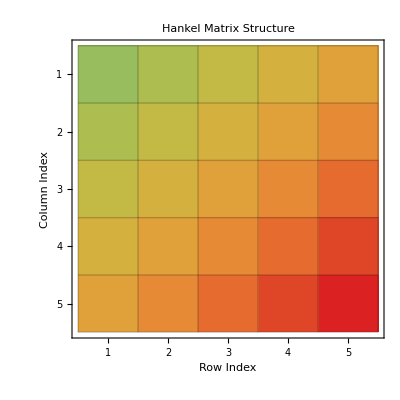

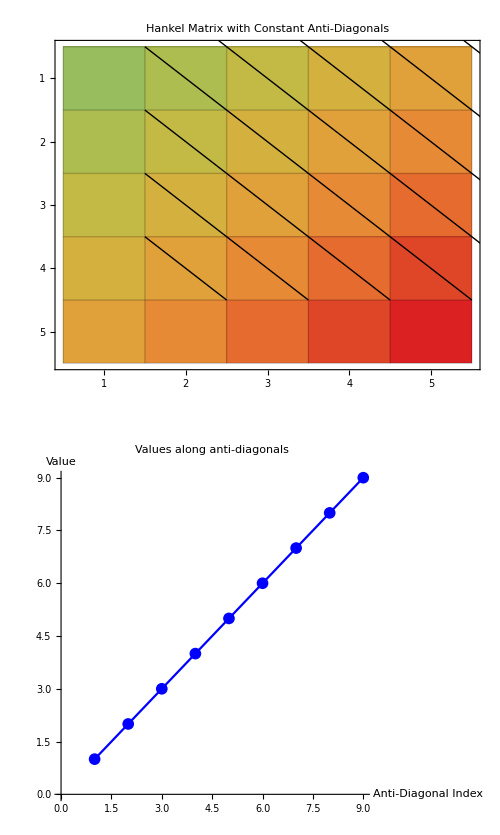

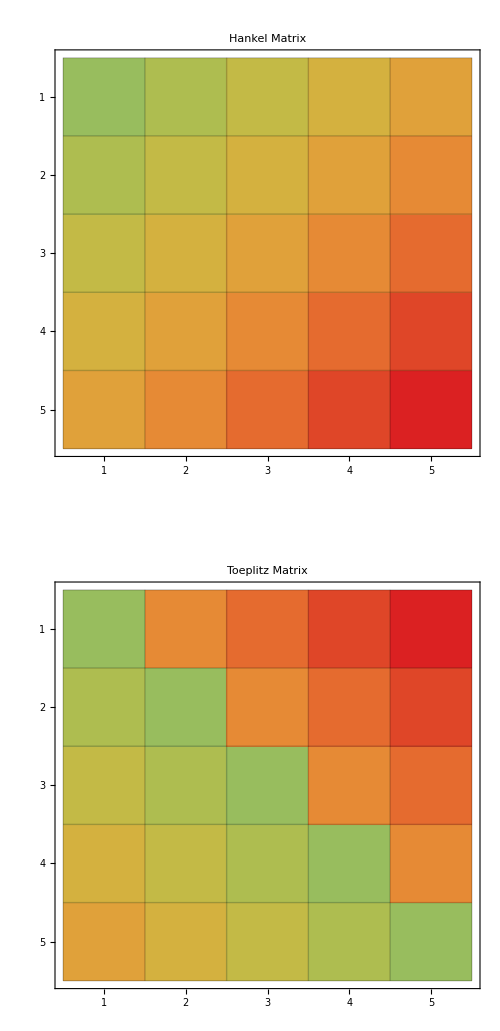

```mathematica
(* Visualize the structure of a Hankel matrix *)
MatrixPlot[H, 
  ColorFunction -> "Rainbow",
  PlotLabel -> "Hankel Matrix Structure",
  Mesh -> All,
  MeshStyle -> Opacity[0.2],
  FrameLabel -> {{"Row Index", None}, {"Column Index", None}}]

(* Visualize anti-diagonals *)
n = Dimensions[H][[1]];
GraphicsGrid[{
  {MatrixPlot[H, 
     ColorFunction -> "Rainbow",
     PlotLabel -> "Hankel Matrix with Constant Anti-Diagonals",
     Epilog -> Table[
       Line[{{j, 1}, {1, j}}], 
       {j, 1, 2*n - 1}],
     Mesh -> All, 
     MeshStyle -> Opacity[0.2]]},
  {ListLinePlot[values, 
     PlotLabel -> "Values along anti-diagonals",
     AxesLabel -> {"Anti-Diagonal Index", "Value"},
     PlotStyle -> Blue,
     PlotMarkers -> {"●", 12}]}
}, ImageSize -> 500]

(* Comparison between Hankel and Toeplitz matrices *)
GraphicsGrid[{
  {MatrixPlot[H, 
     ColorFunction -> "Rainbow",
     PlotLabel -> "Hankel Matrix",
     Mesh -> All, 
     MeshStyle -> Opacity[0.2]]},
  {MatrixPlot[T, 
     ColorFunction -> "Rainbow",
     PlotLabel -> "Toeplitz Matrix",
     Mesh -> All, 
     MeshStyle -> Opacity[0.2]]}
}, ImageSize -> 500]
```

### Circulant Matrices

A circulant matrix is a special type of Toeplitz matrix where each row is a cyclic shift of the row above it. For an  circulant matrix , the entries satisfy:



The general form of an  circulant matrix is:

-Graphics-

Circulant matrices are completely determined by  values: . Key properties of circulant matrices include:

The sum of two circulant matrices is circulant

The product of two circulant matrices is circulant and commutative

All circulant matrices share the same eigenvectors (the Fourier basis)

The eigenvalues of a circulant matrix are given by the Discrete Fourier Transform (DFT) of its first row

Circulant matrices can be diagonalized by the DFT matrix: C = F^{-1} \Lambda F where F is the DFT matrix

Systems involving circulant matrices can be solved in O(n \log n) time using Fast Fourier Transform (FFT)

Circulant matrices appear in signal processing (circular convolution), differential equations with periodic boundary conditions, and image processing.

```mathematica
(* Example *)
c = {1, 2, 3, 4, 5};
Circ = CirculantMatrix[c];
Print["Circulant Matrix:"]
MatrixForm[Circ]

(* Verify the circulant property *)
Print["Checking circulant property:"]
isCirculant = And @@ Flatten[Table[
  Circ[[i, j]] == Circ[[Mod[i, Length[c]] + 1, Mod[j, Length[c]] + 1]],
  {i, 1, Length[c]}, {j, 1, Length[c]}
]];
Print["Matrix satisfies circulant property? ", isCirculant]

(* Eigenvalue decomposition via DFT *)
n = Length[c];
F = Table[Exp[-2*Pi*I*j*k/n]/Sqrt[n], {j, 0, n-1}, {k, 0, n-1}];
Print["DFT Matrix F:"]
MatrixForm[F // N]

(* Eigenvalues via DFT *)
eigenvalues = Sqrt[n] * Fourier[c];
Print["Eigenvalues via DFT:"]
eigenvalues // N

(* Direct eigenvalue calculation *)
directEigen = Eigenvalues[Circ];
Print["Eigenvalues via direct calculation:"]
directEigen // N

(* Sorting both sets to compare *)
Print["Max difference between eigenvalues computed via DFT and direct calculation:"]
Max[Abs[Sort[Re[eigenvalues]] - Sort[Re[directEigen]]]] // N

(* Demonstration of fast matrix-vector multiplication via FFT *)
v = RandomReal[1, n];

(* Standard multiplication *)
result1 =Circ.v;

(* Multiplication via FFT *)
result2 = InverseFourier[Fourier[c] * Fourier[v]];

Print["Maximum difference between standard and FFT multiplication:"]
Max[Abs[result1 - result2]] // N
```

Circulant Matrix:

CirculantMatrix[{1,2,3,4,5}]

Checking circulant property:

Part::partw: Part 2 of CirculantMatrix[{1,2,3,4,5}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Matrix satisfies circulant property? 1==CirculantMatrix[{1,2,3,4,5}]⟦2,2⟧&&2==CirculantMatrix[{1,2,3,4,5}]⟦2,3⟧&&3==CirculantMatrix[{1,2,3,4,5}]⟦2,4⟧&&4==CirculantMatrix[{1,2,3,4,5}]⟦2,5⟧&&5==CirculantMatrix[{1,2,3,4,5}]⟦2,1⟧&&CirculantMatrix[{1,2,3,4,5}]⟦2,1⟧==CirculantMatrix[{1,2,3,4,5}]⟦3,2⟧&&CirculantMatrix[{1,2,3,4,5}]⟦2,2⟧==CirculantMatrix[{1,2,3,4,5}]⟦3,3⟧&&CirculantMatrix[{1,2,3,4,5}]⟦2,3⟧==CirculantMatrix[{1,2,3,4,5}]⟦3,4⟧&&CirculantMatrix[{1,2,3,4,5}]⟦2,4⟧==CirculantMatrix[{1,2,3,4,5}]⟦3,5⟧&&CirculantMatrix[{1,2,3,4,5}]⟦2,5⟧==CirculantMatrix[{1,2,3,4,5}]⟦3,1⟧&&CirculantMatrix[{1,2,3,4,5}]⟦3,1⟧==CirculantMatrix[{1,2,3,4,5}]⟦4,2⟧&&CirculantMatrix[{1,2,3,4,5}]⟦3,2⟧==CirculantMatrix[{1,2,3,4,5}]⟦4,3⟧&&CirculantMatrix[{1,2,3,4,5}]⟦3,3⟧==CirculantMatrix[{1,2,3,4,5}]⟦4,4⟧&&CirculantMatrix[{1,2,3,4,5}]⟦3,4⟧==CirculantMatrix[{1,2,3,4,5}]⟦4,5⟧&&CirculantMatrix[{1,2,3,4,5}]⟦3,5⟧==CirculantMatrix[{1,2,3,4,5}]⟦4,1⟧&&CirculantMatrix[{1,2,3,4,5}]⟦4,1⟧==CirculantMatrix[{1,2,3,4,5}]⟦5,2⟧&&CirculantMatrix[{1,2,3,4,5}]⟦4,2⟧==CirculantMatrix[{1,2,3,4,5}]⟦5,3⟧&&CirculantMatrix[{1,2,3,4,5}]⟦4,3⟧==CirculantMatrix[{1,2,3,4,5}]⟦5,4⟧&&CirculantMatrix[{1,2,3,4,5}]⟦4,4⟧==CirculantMatrix[{1,2,3,4,5}]⟦5,5⟧&&CirculantMatrix[{1,2,3,4,5}]⟦4,5⟧==CirculantMatrix[{1,2,3,4,5}]⟦5,1⟧&&CirculantMatrix[{1,2,3,4,5}]⟦5,1⟧==2&&CirculantMatrix[{1,2,3,4,5}]⟦5,2⟧==3&&CirculantMatrix[{1,2,3,4,5}]⟦5,3⟧==4&&CirculantMatrix[{1,2,3,4,5}]⟦5,4⟧==5&&CirculantMatrix[{1,2,3,4,5}]⟦5,5⟧==1

DFT Matrix F:

(0.447214 | 0.447214 | 0.447214 | 0.447214 | 0.447214
0.447214 | 0.138197-0.425325 ⅈ | -0.361803-0.262866 ⅈ | -0.361803+0.262866 ⅈ | 0.138197+0.425325 ⅈ
0.447214 | -0.361803-0.262866 ⅈ | 0.138197+0.425325 ⅈ | 0.138197-0.425325 ⅈ | -0.361803+0.262866 ⅈ
0.447214 | -0.361803+0.262866 ⅈ | 0.138197-0.425325 ⅈ | 0.138197+0.425325 ⅈ | -0.361803-0.262866 ⅈ
0.447214 | 0.138197+0.425325 ⅈ | -0.361803+0.262866 ⅈ | -0.361803-0.262866 ⅈ | 0.138197-0.425325 ⅈ)

Eigenvalues via DFT:

{15.+0. ⅈ,-2.5-3.44095 ⅈ,-2.5-0.812299 ⅈ,-2.5+0.812299 ⅈ,-2.5+3.44095 ⅈ}

Eigenvalues via direct calculation:

Eigenvalues[CirculantMatrix[{1.,2.,3.,4.,5.}]]

Max difference between eigenvalues computed via DFT and direct calculation:

Max[Abs[-2.5-1. Re[Eigenvalues[CirculantMatrix[{1.,2.,3.,4.,5.}]]]],Abs[15.-1. Re[Eigenvalues[CirculantMatrix[{1.,2.,3.,4.,5.}]]]]]

Maximum difference between standard and FFT multiplication:

Max[Abs[-3.92093+CirculantMatrix[{1.,2.,3.,4.,5.}].{0.267784,0.980623,0.578695,0.179749,0.37127}],Abs[-3.45619+CirculantMatrix[{1.,2.,3.,4.,5.}].{0.267784,0.980623,0.578695,0.179749,0.37127}],Abs[-3.22284+CirculantMatrix[{1.,2.,3.,4.,5.}].{0.267784,0.980623,0.578695,0.179749,0.37127}],Abs[-2.79172+CirculantMatrix[{1.,2.,3.,4.,5.}].{0.267784,0.980623,0.578695,0.179749,0.37127}],Abs[-2.56125+CirculantMatrix[{1.,2.,3.,4.,5.}].{0.267784,0.980623,0.578695,0.179749,0.37127}]]

MatrixPlot::mat0: Argument CirculantMatrix[{1,2,3,4,5}] at position 1 is not a matrix.

MatrixPlot[CirculantMatrix[{1,2,3,4,5}],ColorFunction→Rainbow,PlotLabel→Circulant Matrix Structure,Mesh→All,MeshStyle→Opacity[0.2],FrameLabel→{{Row Index,None},{Column Index,None}}]

StringForm::sfq: Unmatched backquote in Eigenvector ``, ω^`.

General::stop: Further output of StringForm::sfq will be suppressed during this calculation.

-Graphics-

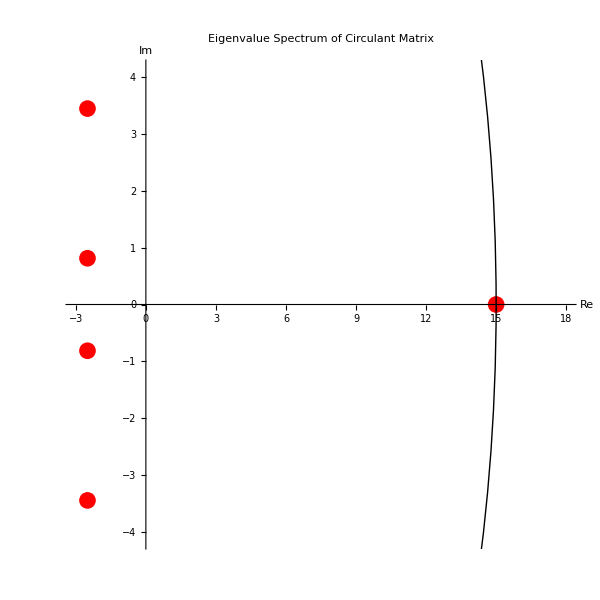

MatrixPlot::mat0: Argument CirculantMatrix[{1,2,3,4,5}] at position 1 is not a matrix.

General::stop: Further output of MatrixPlot::mat0 will be suppressed during this calculation.

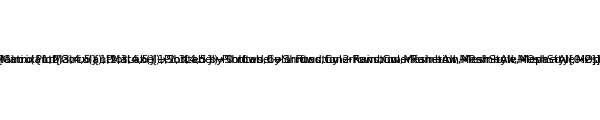

```mathematica
(* Visualize the structure of a circulant matrix *)
MatrixPlot[Circ, 
  ColorFunction -> "Rainbow",
  PlotLabel -> "Circulant Matrix Structure",
  Mesh -> All,
  MeshStyle -> Opacity[0.2],
  FrameLabel -> {{"Row Index", None}, {"Column Index", None}}]

(* Visualize eigenvectors (columns of F) *)
n = Length[c];
eigVecPlots = Table[
  ListLinePlot[
    {Re[F[[All, j]]], Im[F[[All, j]]]},
    PlotLabel -> StringForm["Eigenvector ``, ω^`", j, j-1],
    PlotLegends -> {"Real part", "Imaginary part"},
    PlotStyle -> {Blue, Red},
    AxesLabel -> {"Index", "Value"},
    PlotRange -> {{0, n+1}, {-0.7, 0.7}}
  ],
  {j, 1, Min[n, 4]}
];

GraphicsGrid[Partition[eigVecPlots, 2], ImageSize -> 600]

(* Visualize the eigenvalue spectrum *)
ListPlot[
  ReIm[eigenvalues],
  PlotLabel -> "Eigenvalue Spectrum of Circulant Matrix",
  AxesLabel -> {"Re", "Im"},
  PlotStyle -> {Red, PointSize[0.02]},
  PlotRange -> 1.2 * {{Min[Re[eigenvalues]], Max[Re[eigenvalues]]}, 
                   {Min[Im[eigenvalues]], Max[Im[eigenvalues]]}},
  AspectRatio -> 1,
  Epilog -> {Circle[{0, 0}, Max[Abs[eigenvalues]]]}
]

(* Demonstrate the circulant property with a shift operation *)
GraphicsRow[
  Table[
    MatrixPlot[
      RotateLeft[Circ, k],
      PlotLabel -> StringForm["Shifted by `` rows", k],
      ColorFunction -> "Rainbow",
      Mesh -> All,
      MeshStyle -> Opacity[0.2]
    ],
    {k, 0, 2}
  ],
  ImageSize -> 600
]
```

These structured matrices (Toeplitz, Hankel, and Circulant) are particularly valuable in computational linear algebra because they:

Require significantly less storage than general matrices (O(n) vs O(n.b2))

Allow for faster algorithms for operations like matrix-vector multiplication and solving linear systems

Preserve their structure under certain operations, allowing for specialized algorithms

Arise naturally in many practical applications, particularly those involving signals, time series, and systems with special types of symmetry

By exploiting these structures, we can develop much more efficient computational methods for large-scale problems that would be intractable with general matrix algorithms.

## Sparse

### Definition

Sparse matrices are matrices where the majority of elements are zero. More formally, an  matrix is considered sparse when the number of non-zero elements is significantly smaller than the total number of elements . While there’s no strict mathematical threshold for “sparseness,” matrices where the number of non-zero entries is  or  are typically considered sparse.

The significance of sparse matrices in computational linear algebra cannot be overstated. By focusing only on the non-zero elements, we can dramatically reduce:

Memory requirements for storage

Computational complexity for matrix operations

Execution time for algorithms

Sparsity patterns can arise naturally in many applications:

Network adjacency matrices

Partial differential equations discretized on grids

Finite element methods

Natural language processing term-document matrices

Web link structures

Large-scale optimization problems

Special classes of sparse matrices include:

Band matrices (non-zero elements clustered around the diagonal)

Block-diagonal matrices

Tridiagonal matrices (special case of band matrices)

Sparse Toeplitz and circulant matrices

### Storage Schemes and Efficiency

#### Coordinate Format (COO)

The simplest sparse storage format is the coordinate format, which stores a list of (row, column, value) triplets for each non-zero element:

```mathematica
values = Table[{Subscript[val, i],Subscript[row, i],Subscript[cols, i]},{i,1,10}]
```

{{val_1,row_1,cols_1},{val_2,row_2,cols_2},{val_3,row_3,cols_3},{val_4,row_4,cols_4},{val_5,row_5,cols_5},{val_6,row_6,cols_6},{val_7,row_7,cols_7},{val_8,row_8,cols_8},{val_9,row_9,cols_9},{val_10,row_10,cols_10}}

Advantages :

Simple to implement

Efficient for incrementally building a matrix

Handles any sparsity pattern

Disadvantages :

Not optimal for matrix operations

Requires sorting for efficient operations

#### Compressed Sparse Row (CSR)

The CSR format stores :

An array of non - zero values

An array of column indices for each value

An array of row pointers indicating where each row starts in the values array

```mathematica
valuse = Table[Subscript[vals, i],{i,1,10}]
rowPointers = Table[Subscript[pointer, i],{i,1,10}]
columns = Table[Subscript[cols, i],{i,1,10}]
```

{vals_1,vals_2,vals_3,vals_4,vals_5,vals_6,vals_7,vals_8,vals_9,vals_10}

{pointer_1,pointer_2,pointer_3,pointer_4,pointer_5,pointer_6,pointer_7,pointer_8,pointer_9,pointer_10}

{cols_1,cols_2,cols_3,cols_4,cols_5,cols_6,cols_7,cols_8,cols_9,cols_10}

Advantages :

Efficient row-wise traversal

Good for sparse matrix-vector multiplication

Memory efficient.

Disadvantages :

Column access is expensive

Less efficient for dynamic construction

#### Compressed Sparse Column (CSC)

The CSC format is similar to CSR but optimized for column access :

An array of non-zero values

An array of row indices for each value

An array of column pointers

```mathematica
valuse = Table[Subscript[vals, i],{i,1,10}]
rows = Table[Subscript[row, i],{i,1,10}]
columnPointers = Table[Subscript[pointer, i],{i,1,10}]
```

{vals_1,vals_2,vals_3,vals_4,vals_5,vals_6,vals_7,vals_8,vals_9,vals_10}

{row_1,row_2,row_3,row_4,row_5,row_6,row_7,row_8,row_9,row_10}

{pointer_1,pointer_2,pointer_3,pointer_4,pointer_5,pointer_6,pointer_7,pointer_8,pointer_9,pointer_10}

Advantages :

Efficient column-wise traversal

Good for operations like matrix transposition

Disadvantages :

Row access is expensive

#### Block Compressed Sparse Row (BCSR)

For matrices with block - wise sparsity patterns, BCSR stores small dense blocks :

Each block is stored as a dense submatrix

Only the positions of non - zero blocks are recorded

Advantages:

Can leverage cache efficiency for block operations

Good for matrices with regular block structure

Disadvantages:

May waste space if blocks are not fully dense

#### Storage Efficiency Comparison

For a matrix with dimensions  and  non - zero elements :

Dense storage: Requires  elements

COO format: Requires  elements (values, row indices, column indices)

CSR/CSC format: Requires  elements

Band storage (for band matrices): Requires  elements, where  is the bandwidth

Memory savings are substantial when . For example, in a  matrix with  non - zero elements :

Dense storage:  elements ( TB with double precision)

CSR storage: 2 elements ( MB with double precision)

This represents a compression ratio of approximately !

### Sparse Matrix in Mathematica

```mathematica
(* Create a sparse matrix *)
n = 1000;
density = 0.01; (* 1% of elements are non-zero *)
nnz = Round[n^2 * density]; (* Number of non-zero elements *)

(* Random sparse matrix using built-in SparseArray *)
positions = RandomInteger[{1, n}, {nnz, 2}];
values = RandomReal[{-1, 1}, nnz];
sparseMatrix = SparseArray[positions -> values, {n, n}];

(* Information about the sparse matrix *)
Print["Matrix dimensions: ", Dimensions[sparseMatrix]]
Print["Number of non-zero elements: ", Length[sparseMatrix["NonzeroValues"]]]
Print["Density: ", Length[sparseMatrix["NonzeroValues"]]/(n^2) * 100, "%"]

(* Demonstrate storage efficiency *)
bytesRequired = ByteCount[sparseMatrix];
denseVersion = Normal[sparseMatrix];
denseBytesRequired = ByteCount[denseVersion];

Print["Memory usage (sparse): ", bytesRequired/1024^2, " MB"]
Print["Memory usage (dense): ", denseBytesRequired/1024^2, " MB"]
Print["Compression ratio: ", N[denseBytesRequired/bytesRequired]]

(* Manual implementation of storage formats *)
(* COO format *)
cooValues = sparseMatrix["NonzeroValues"];
cooPositions = sparseMatrix["NonzeroPositions"];
cooRows = cooPositions[[All, 1]];
cooCols = cooPositions[[All, 2]];

Print["COO format storage size: ", 
  (ByteCount[cooValues] + ByteCount[cooRows] + ByteCount[cooCols])/1024^2, " MB"]

(* CSR format simulation *)
(* Sort by row then column for CSR-like order *)
sortedOrder = Ordering[cooRows*n + cooCols];
csrValues = cooValues[[sortedOrder]];
csrCols = cooCols[[sortedOrder]];
csrRowPtr = Prepend[Accumulate[Tally[cooRows][[All, 2]]], 0];

Print["CSR format storage size: ", 
  (ByteCount[csrValues] + ByteCount[csrCols] + ByteCount[csrRowPtr])/1024^2, " MB"]

(* Sparse matrix operations *)
(* Matrix-Vector multiplication *)
v = RandomReal[1, n];

(* Time comparison *)
Print["Sparse matrix-vector multiplication time:"]
sparseTime = First[Timing[sparseResult = sparseMatrix.v;]];
Print["  Sparse: ", sparseTime, " seconds"]
denseTime = First[Timing[denseResult = denseVersion.v;]];
Print["  Dense: ", denseTime, " seconds"]
Print["  Speedup: ", denseTime/sparseTime, "x"]

(* Accuracy verification *)
Print["Max difference between sparse and dense multiplication: ", 
  Max[Abs[sparseResult - denseResult]]]
```

Matrix dimensions: {1000,1000}

Number of non-zero elements: 9950

Density: 199/200%

Memory usage (sparse): 10505/65536 MB

Memory usage (dense): 23633/1024 MB

Compression ratio: 143.98

COO format storage size: 29925/131072 MB

CSR format storage size: 20987/131072 MB

Sparse matrix-vector multiplication time:

Sparse: 0.000399 seconds

Dense: 0.007092 seconds

Speedup: 17.7744x

Max difference between sparse and dense multiplication: 4.44089×10^-16

### Visualization

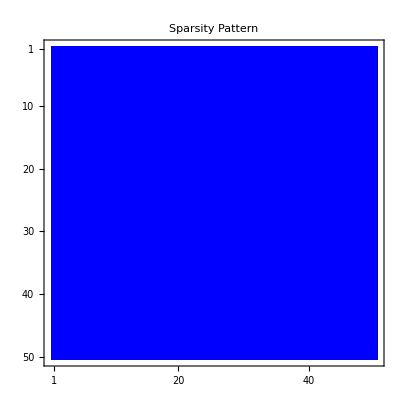

SparseArray::bndtr: There are insufficient positions available in the Band[{1,1},{50,50},{5,5}] to fit all the values {-0.440014,0.726611,0.245263,0.0602196,0.00604301,-0.347096,0.0169604,-0.643906,-0.960509,0.90476,«240»} so some of the values will be omitted in the specification Band[{1,1},{50,50},{5,5}]→{-0.440014,0.726611,0.245263,0.0602196,0.00604301,-0.347096,0.0169604,-0.643906,-0.960509,0.90476,«240»}.

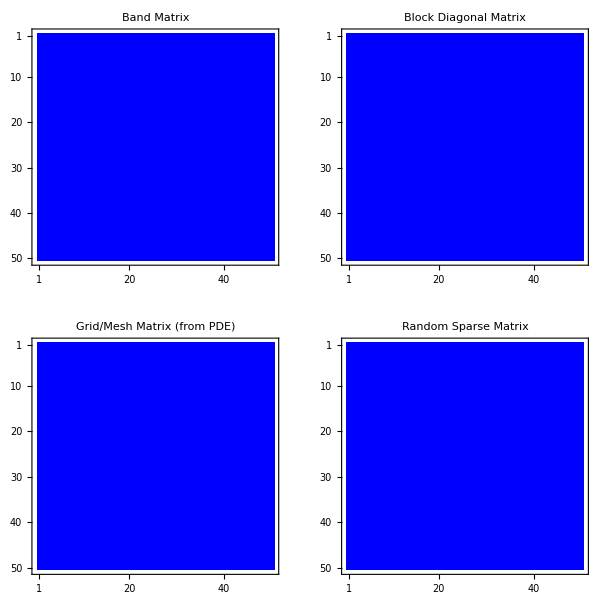

Values::invrl: The argument {-0.843636,-0.739233,-0.448231,-0.0785709,-0.693779,-0.808889,0.744587,-0.0220205,0.377376,0.94097,«229»} is not a valid Association or a list of rules.

Prepend::invdt: The argument 0 is not a rule or a list of rules.

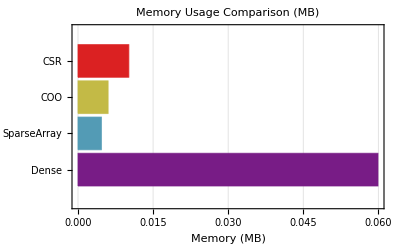

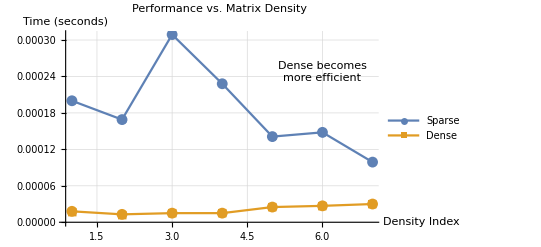

```mathematica
(*Create a smaller sparse matrix for visualization*)n=50;
density=0.1;
nnz=Round[n^2*density];
positions=RandomInteger[{1,n},{nnz,2}];
values=RandomReal[{-1,1},nnz];
smallSparseMatrix=SparseArray[positions->values,{n,n}];

(*Visualize the sparsity pattern*)
MatrixPlot[smallSparseMatrix,PlotLabel->"Sparsity Pattern",ColorFunction->(If[#==0,White,Blue]&)]

(*Create different sparsity patterns*)
(*Band matrix*)
bandMatrix=SparseArray[{Band[{1,1}]->2,(*Main diagonal*)Band[{1,2}]->-1,(*Upper diagonal*)Band[{2,1}]->-1     (*Lower diagonal*)},{n,n}];

(*Block diagonal matrix*)
blockSize=5;
blocks=Table[RandomReal[{-1,1},{blockSize,blockSize}],{i,1,Quotient[n,blockSize]}];
blockDiagMatrix=SparseArray[Band[{1,1},{n,n},{blockSize,blockSize}]->Flatten[blocks]];

(*Grid/mesh matrix (from 2D discretized PDE)*)
gridMatrix=SparseArray[{Band[{1,1}]->4,(*Main diagonal*)Band[{1,2}]->-1,(*Upper diagonal*)Band[{2,1}]->-1,(*Lower diagonal*)Band[{1,Ceiling[Sqrt[n]]+1}]->-1,(*Upper far diagonal*)Band[{Ceiling[Sqrt[n]]+1,1}]->-1   (*Lower far diagonal*)},{n,n}];

(*Visualize different sparsity patterns*)
GraphicsGrid[{{MatrixPlot[bandMatrix,PlotLabel->"Band Matrix",ColorFunction->(If[#==0,White,Blue]&)],MatrixPlot[blockDiagMatrix,PlotLabel->"Block Diagonal Matrix",ColorFunction->(If[#==0,White,Blue]&)]},{MatrixPlot[gridMatrix,PlotLabel->"Grid/Mesh Matrix (from PDE)",ColorFunction->(If[#==0,White,Blue]&)],MatrixPlot[smallSparseMatrix,PlotLabel->"Random Sparse Matrix",ColorFunction->(If[#==0,White,Blue]&)]}},ImageSize->600]

(*Generate a random sparse matrix for memory usage*)
density=0.1;
nnz=Round[n^2*density];
positions=RandomInteger[{1,n},{nnz,2}];
values=RandomReal[{-1,1},nnz];
sparseMatrix=SparseArray[positions->values,{n,n}];
denseMatrix=Normal[sparseMatrix];

(*COO format*)
cooValues=Values[sparseMatrix["NonzeroValues"]];
cooPositions=sparseMatrix["NonzeroPositions"];
cooRows=cooPositions[[All,1]];
cooCols=cooPositions[[All,2]];

(*CSR format*)
csrValues=cooValues;
csrCols=cooCols;
csrRowPtr=Accumulate[Prepend[Counts[cooRows],0]];

(*Memory usage*)
denseBytesRequired=ByteCount[denseMatrix];
bytesRequired=ByteCount[sparseMatrix];

memoryData={{"Dense",denseBytesRequired/1024.^2},{"SparseArray",bytesRequired/1024.^2},{"COO",(ByteCount[cooValues]+ByteCount[cooRows]+ByteCount[cooCols])/1024.^2},{"CSR",(ByteCount[csrValues]+ByteCount[csrCols]+ByteCount[csrRowPtr])/1024.^2}};

BarChart[memoryData[[All,2]],ChartLabels->memoryData[[All,1]],PlotLabel->"Memory Usage Comparison (MB)",AxesLabel->{"Storage Format","Memory (MB)"},PlotTheme->"Detailed",BarOrigin->Left,ChartStyle->"Rainbow"]

(*Visualize performance vs.density*)
densities={0.001,0.01,0.05,0.1,0.2,0.5,0.8};
sparseTimes={};
denseTimes={};

v=RandomReal[{-1,1},n];

For[i=1,i<=Length[densities],i++,density=densities[[i]];
nnz=Round[n^2*density];
positions=DeleteDuplicates[RandomInteger[{1,n},{nnz,2}]];
values=RandomReal[{-1,1},Length[positions]];
matrix=SparseArray[positions->values,{n,n}];
denseMatrix=Normal[matrix];
sparseTime=First@AbsoluteTiming[matrix.v];
denseTime=First@AbsoluteTiming[denseMatrix.v];
AppendTo[sparseTimes,sparseTime];
AppendTo[denseTimes,denseTime];]

ListLinePlot[{sparseTimes,denseTimes},PlotLegends->{"Sparse","Dense"},AxesLabel->{"Density Index","Time (seconds)"},PlotLabel->"Performance vs. Matrix Density",Mesh->All,PlotMarkers->{"●","■"},PlotRange->All,GridLines->Automatic,Epilog->{Text["Dense becomes\nmore efficient",{6,0.8*Max[Join[sparseTimes,denseTimes]]}]}]
```

### Application

#### Finite Element Method

In FEM, the domain is discretized into a mesh of elements. The resulting system of equations typically has a sparse structure because each element only interacts with its neighbors.

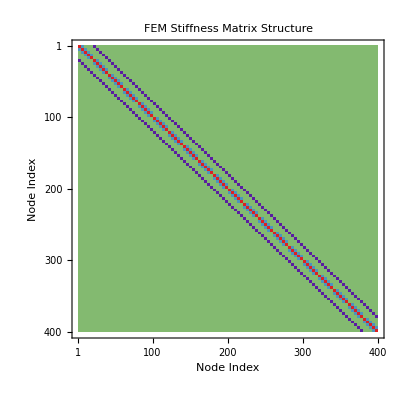

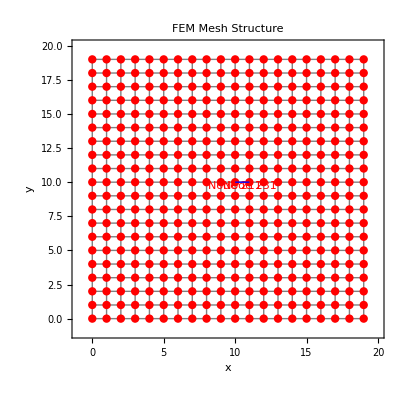

```mathematica
(* Create a simple FEM-like matrix for a 2D heat equation on a square domain *)
n = 20; (* Grid size n×n *)
totalNodes = n^2;
h = 1/(n-1); (* Grid spacing *)

(* Create the stiffness matrix *)
femMatrix = SparseArray[{}, {totalNodes, totalNodes}];

For[i = 0, i < n, i++,
  For[j = 0, j < n, j++,
    node = i*n + j + 1;
    
    (* Add diagonal entry *)
    femMatrix[[node, node]] = 4;
    
    (* Connect to neighbors *)
    If[i > 0, femMatrix[[node, (i-1)*n + j + 1]] = -1];
    If[i < n-1, femMatrix[[node, (i+1)*n + j + 1]] = -1];
    If[j > 0, femMatrix[[node, i*n + (j-1) + 1]] = -1];
    If[j < n-1, femMatrix[[node, i*n + (j+1) + 1]] = -1];
  ]
]

(* Scale by 1/h^2 *)
femMatrix = femMatrix / h^2;

(* Visualize the FEM matrix structure *)
MatrixPlot[femMatrix, 
  PlotLabel -> "FEM Stiffness Matrix Structure",
  ColorFunction -> (If[# == 0, White, ColorData["Rainbow"][#]] &),
  FrameLabel -> {{"Node Index", None}, {"Node Index", None}}]

(* Demonstrate how the FEM mesh maps to matrix structure *)
meshGrid = Table[{i, j}, {i, 0, n-1}, {j, 0, n-1}];
meshPoints = Flatten[meshGrid, 1];

Graphics[{
  Gray, Line[Table[{{i, 0}, {i, n-1}}, {i, 0, n-1}]],
  Gray, Line[Table[{{0, j}, {n-1, j}}, {j, 0, n-1}]],
  Red, PointSize[0.015], Point[meshPoints],
  Blue, Line[{{n/2, n/2}, {n/2 + 1, n/2}}], (* Sample connection *)
  Red, Text["Node " <> ToString[(n/2)*n + (n/2) + 1], {n/2, n/2 - 0.3}],
  Red, Text["Node " <> ToString[(n/2 + 1)*n + (n/2) + 1], {n/2 + 1, n/2 - 0.3}]
},
PlotLabel -> "FEM Mesh Structure",
Frame -> True,
FrameLabel -> {{"y", None}, {"x", None}},
PlotRange -> {{-1, n}, {-1, n}}]
```

#### Network and Graph Analysis

Adjacency matrices of real-world networks are typically very sparse. For a network with millions of nodes, storing the full adjacency matrix would be impossible without sparse representations.

Network properties:

Number of nodes: 100

Number of edges: 197

Network density: 197/4950

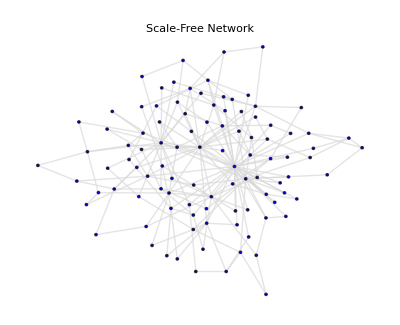

```mathematica
(* Create a scale-free network (common in real-world scenarios) *)
n = 100; (* Number of nodes *)
m = 2;   (* Number of edges to attach from a new node to existing nodes *)
g = RandomGraph[BarabasiAlbertGraphDistribution[n, m]];

(* Get the adjacency matrix *)
adjMatrix = AdjacencyMatrix[g];

Print["Network properties:"]
Print["Number of nodes: ", VertexCount[g]]
Print["Number of edges: ", EdgeCount[g]]
Print["Network density: ", EdgeCount[g]/(VertexCount[g]*(VertexCount[g]-1)/2)]

(*Visualize the network and its adjacency matrix*)GraphicsRow[{GraphPlot[g,PlotLabel->"Scale-Free Network",VertexSize->0.3,EdgeStyle->LightGray,VertexStyle->Blue],MatrixPlot[adjMatrix,PlotLabel->"Adjacency Matrix",ColorFunctionScaling->False]},ImageSize->600]


(* Perform a common network analysis: PageRank *)
(* PageRank involves power iteration with a sparse transition matrix *)
pageRankVector = PageRankCentrality[g];
```

#### Natural Language Processing (NLP)

In NLP, term - document matrices are extremely sparse because most words appear in only a small fraction of documents .

Term-Document Matrix:

Dimensions: {1000,100}

Non-zero entries: 6524

Density: 1631/250%

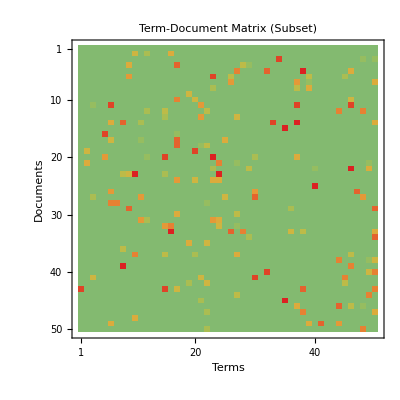

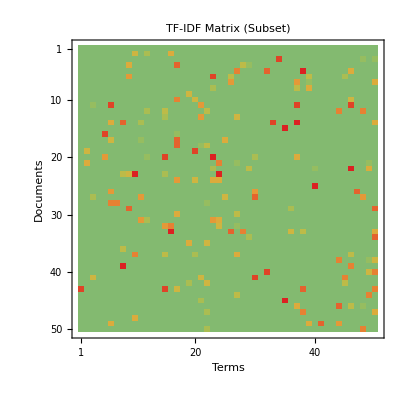

```mathematica
(* Simulate a term-document matrix with 100 documents and 1000 terms *)
nDocs = 100;
nTerms = 1000;
averageTermsPerDoc = 50; (* Each document uses about 50 unique terms *)

(* Generate sparse term-document matrix *)
termDocMatrix = SparseArray[{}, {nTerms, nDocs}];

(* Fill with random data - each document has a small subset of terms *)
For[doc = 1, doc <= nDocs, doc++,
  (* Select random terms for this document *)
  docTerms = RandomSample[Range[nTerms], RandomInteger[{30, averageTermsPerDoc * 2}]];
  
  (* Assign random term frequencies *)
  For[i = 1, i <= Length[docTerms], i++,
    term = docTerms[[i]];
    (* Term frequency follows Zipf's law - a few terms appear frequently *)
    frequency = RandomInteger[{1, 10}];
    termDocMatrix[[term, doc]] = frequency;
  ]
]

(* Analyze sparsity *)
Print["Term-Document Matrix:"]
Print["Dimensions: ", Dimensions[termDocMatrix]]
Print["Non-zero entries: ", Length[termDocMatrix["NonzeroValues"]]]
Print["Density: ", Length[termDocMatrix["NonzeroValues"]]/(nTerms*nDocs) * 100, "%"]

(* Visualize the term-document matrix *)
(* We'll visualize a smaller subset for clarity *)
subsetSize = 50;
subsetTermDocMatrix = termDocMatrix[[1 ;; subsetSize, 1 ;; subsetSize]];

MatrixPlot[subsetTermDocMatrix, 
  PlotLabel -> "Term-Document Matrix (Subset)",
  ColorFunction -> (If[# == 0, White, ColorData["Rainbow"][#]] &),
  FrameLabel -> {{"Terms", None}, {"Documents", None}}]

(* Compute Term Frequency-Inverse Document Frequency (TF-IDF) *)
(* A common transformation in NLP that benefits from sparse representation *)
docFrequencies = Table[
  Count[termDocMatrix[[term, All]], x_ /; x > 0],
  {term, 1, nTerms}
];

idf = Log[nDocs/(docFrequencies +0.01)];

(* Apply TF-IDF transformation *)
tfidfMatrix = SparseArray[{}, Dimensions[termDocMatrix]];
nonZeros = termDocMatrix["NonzeroPositions"];
values = termDocMatrix["NonzeroValues"];

For[i = 1, i <= Length[nonZeros], i++,
  {term, doc} = nonZeros[[i]];
  tf = values[[i]];
  tfidfMatrix[[term, doc]] = tf * idf[[term]];
]

(* Visualize the TF-IDF weights *)
subsetTfidfMatrix = tfidfMatrix[[1 ;; subsetSize, 1 ;; subsetSize]];

MatrixPlot[subsetTfidfMatrix, 
  PlotLabel -> "TF-IDF Matrix (Subset)",
  ColorFunction -> (If[# == 0, White, ColorData["Rainbow"][#]] &),
  FrameLabel -> {{"Terms", None}, {"Documents", None}}]
```

#### Linear Programming and Optimization

Many large - scale optimization problems involve sparse constraint matrices .

Linear Programming Constraint Matrix:

Dimensions: {300,500}

Non-zero entries: 24403

Density: 24403/1500%

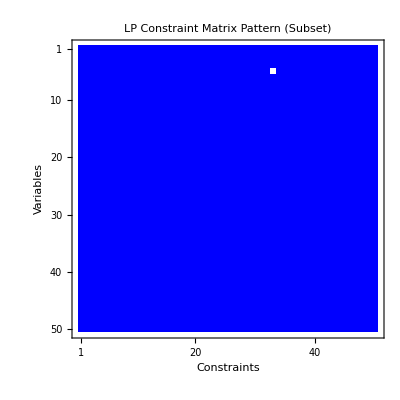

In a real LP solver, sparse algorithms would exploit this structure for:

1. Factorization of the basis matrix

2. Updating the factorization during pivoting

3. Computing search directions

```mathematica
(* Simulate a large linear programming problem *)
nVariables = 500;
nConstraints = 300;
constraintsPerVariable = 50; (* Each variable appears in ~5 constraints *)

(* Generate random sparse constraint matrix *)
constraintMatrix = SparseArray[{}, {nConstraints, nVariables}];

For[var = 1, var <= nVariables, var++,
  (* Select random constraints that involve this variable *)
  varConstraints = RandomSample[Range[nConstraints], RandomInteger[{1, constraintsPerVariable * 2}]];
  
  (* Assign random coefficients *)
  For[i = 1, i <= Length[varConstraints], i++,
    constraint = varConstraints[[i]];
    coef = RandomReal[{-10, 10}];
    constraintMatrix[[constraint, var]] = coef;
  ]
]

(* Create objective function *)
objectiveVector = RandomReal[{-1, 1}, nVariables];

(* Create right-hand side *)
rhs = RandomReal[{0, 100}, nConstraints];

(* Analyze constraint matrix sparsity *)
Print["Linear Programming Constraint Matrix:"]
Print["Dimensions: ", Dimensions[constraintMatrix]]
Print["Non-zero entries: ", Length[constraintMatrix["NonzeroValues"]]]
Print["Density: ", Length[constraintMatrix["NonzeroValues"]]/(nConstraints*nVariables) * 100, "%"]

(* Visualize the constraint matrix pattern *)
subsetConstraintMatrix = constraintMatrix[[1 ;; 50, 1 ;; 50]];

MatrixPlot[subsetConstraintMatrix, 
  PlotLabel -> "LP Constraint Matrix Pattern (Subset)",
  ColorFunction -> (If[# == 0, White, If[# > 0, Blue, Red]] &),
  FrameLabel -> {{"Constraints", None}, {"Variables", None}}]

(* Simulate solving the LP *)
(* Note: Actually solving this would require LinearProgramming function *)
Print["In a real LP solver, sparse algorithms would exploit this structure for:"]
Print["1. Factorization of the basis matrix"]
Print["2. Updating the factorization during pivoting"]
Print["3. Computing search directions"]
```

### Benefits of Sparse Matrix Techniques

Memory Efficiency: Storing only non-zero elements dramatically reduces memory requirements.

Computational Efficiency: Operations focus only on non-zero elements, reducing time complexity.

Scalability: Problems that would be intractable in dense form become solvable.

Specialized Algorithms: Many iterative methods (like Conjugate Gradient and GMRES) are particularly effective for sparse systems.

Parallelization Opportunities: Sparse operations can often be effectively parallelized.

### Challenges in Sparse Matrix Computation

Data Structure Complexity: Managing sparse formats adds implementation complexity.

Format Conversion Overhead: Converting between formats can be expensive.

Load Balancing: Achieving good parallel performance with irregular sparsity patterns is challenging.

Fill-in During Factorization: Direct solvers may generate many new non-zero elements during factorization.

Numerical Stability: Some sparse direct methods face stability challenges for ill-conditioned problems.

Sparse matrix techniques are essential for solving large-scale computational problems across many fields of science and engineering. By exploiting the structure where most elements are zero, we can tackle problems of a scale that would otherwise be computationally infeasible.

## Extensions to Infinite-Dimensional Spaces

## Operators on Hilbert Spaces

Hilbert spaces extend the concept of vector spaces to infinite dimensions while preserving the geometrical intuition of Euclidean spaces . A Hilbert space  is a complete inner product space, meaning it has an inner product operation that induces a norm, and it' s complete with respect to that norm (all Cauchy sequences converge).

Key properties of Hilbert spaces include:

They have an inner product  satisfying conjugate symmetry, linearity, and positive-definiteness

They are complete with respect to the norm induced by the inner product:

They admit orthogonal projections and have orthonormal bases (possibly infinite)

```mathematica
(* Define a simple Hilbert space example - the space of sequences with finite ℓ.b2 norm *)
l2NormSquared[sequence_List] := Total[Abs[sequence]^2]
l2Norm[sequence_List] := Sqrt[l2NormSquared[sequence]]

(* Inner product for sequences *)
innerProduct[seq1_List, seq2_List] := 
  If[Length[seq1] == Length[seq2], 
     Total[seq1 * Conjugate[seq2]], 
     Print["Error: Sequences must have same length"]]

(* Example of finite-dimensional approximation to an infinite sequence space *)
seq1 = {1, 1/2, 1/3, 1/4, 1/5, 1/6, 1/7, 1/8, 1/9, 1/10};
seq2 = {0, 1/2, 2/3, 3/4, 4/5, 5/6, 6/7, 7/8, 8/9, 9/10};

l2Norm[seq1]
innerProduct[seq1, seq2]
```

(√(1968329/5))/504

350339/254016

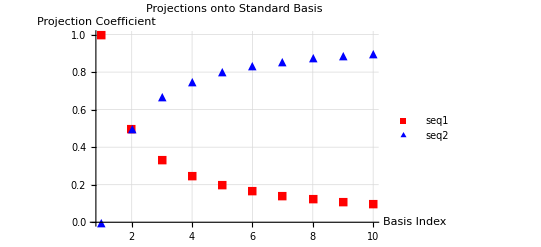

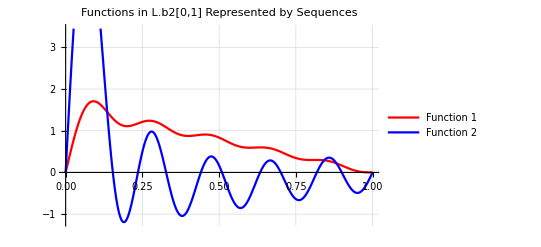

-Graphics- | -Graphics-

```mathematica
(* Visualization of basis elements in a finite-dimensional approximation *)
basisVectors = Table[ReplacePart[ConstantArray[0, 10], i -> 1], {i, 1, 10}];

(* Project a vector onto first few basis elements *)
projectionCoefficients[vec_, basis_] := Table[innerProduct[vec, b], {b, basis}];
coeffs1 = projectionCoefficients[seq1, basisVectors];
coeffs2 = projectionCoefficients[seq2, basisVectors];

(* Visualize the projections *)
projectionPlot = ListPlot[{coeffs1, coeffs2}, 
  PlotStyle -> {{Red, PointSize[0.015]}, {Blue, PointSize[0.015]}},
  PlotLegends -> {"seq1", "seq2"},
  PlotRange -> All,
  AxesLabel -> {"Basis Index", "Projection Coefficient"},
  PlotLabel -> "Projections onto Standard Basis",
  GridLines -> Automatic,
  PlotMarkers -> {"■", "▲"}]

(* Visualize the functions in L.b2[0,1] corresponding to these sequences *)
functionPlot = Plot[{Sum[seq1[[i]]*Sin[i*Pi*x], {i, 1, 10}], 
                    Sum[seq2[[i]]*Sin[i*Pi*x], {i, 1, 10}]}, 
  {x, 0, 1},
  PlotStyle -> {Red, Blue},
  PlotLegends -> {"Function 1", "Function 2"},
  PlotLabel -> "Functions in L.b2[0,1] Represented by Sequences",
  GridLines -> Automatic]

Grid[{{projectionPlot, functionPlot}}]
```

## Bounded Operators

Bounded operators are fundamental in the study of Hilbert spaces. An operator  between Hilbert spaces is bounded if there exists a constant  such that:  for all . These operators are continuous. The set of all bounded operators for a Banach space (check it out). When   the Banach space is an algebra with involution (the adjoint operation). Important classes of bounded operators include Self-adjoint, Normal, Unitary and Compact operators.

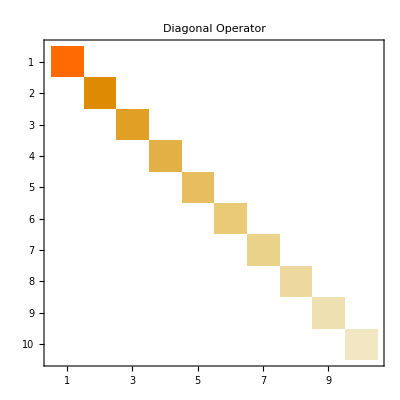

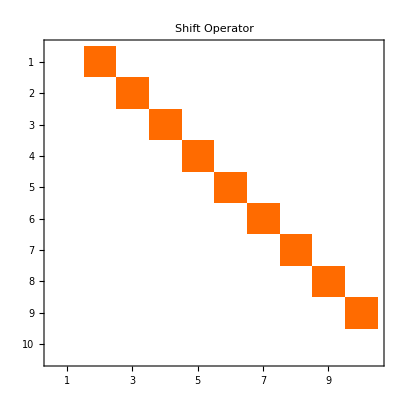

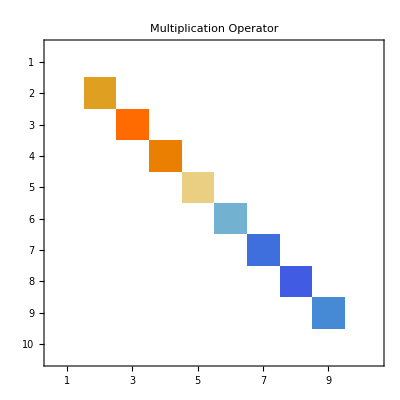

Operator norm of diagonal operator: 1

Operator norm of shift operator: 1

Operator norm of multiplication operator: Cos[π/18]

```mathematica
(* Define a finite-dimensional representation of operators *)
(* Matrix representation of a diagonal operator *)
diagonalOperator[eigenvalues_List] := DiagonalMatrix[eigenvalues]

(* Matrix representation of a shift operator *)
shiftOperator[n_Integer] := 
  SparseArray[{Band[{1, 2}] -> Table[1, {n-1}]}, {n, n}]

(* Matrix representation of a multiplication operator (by a function) *)
multiplicationOperator[f_, gridpoints_List] := DiagonalMatrix[f /@ gridpoints]

(* Check if an operator is bounded (for finite matrices) *)
isBounded[mat_?MatrixQ] := True  (* All finite matrices represent bounded operators *)
operatorNorm[mat_?MatrixQ] := Max[SingularValueList[mat]]  (* Operator norm = largest singular value *)

(* Example operators *)
n = 10;
D1 = diagonalOperator[Table[1/i, {i, 1, n}]];  (* Diagonal operator with decreasing entries *)
S1 = shiftOperator[n];  (* Right shift operator *)
grid = Range[0, 1, 1/(n-1)];
M1 = multiplicationOperator[Sin[2 Pi #]&, grid];  (* Multiplication by sin(2πx) *)

(* Display the operators *)
MatrixPlot[D1, PlotLabel -> "Diagonal Operator"]
MatrixPlot[S1, PlotLabel -> "Shift Operator"]
MatrixPlot[M1, PlotLabel -> "Multiplication Operator"]

(* Calculate operator norms *)
Print["Operator norm of diagonal operator: ", operatorNorm[D1]]
Print["Operator norm of shift operator: ", operatorNorm[S1]]
Print["Operator norm of multiplication operator: ", operatorNorm[M1]]
```

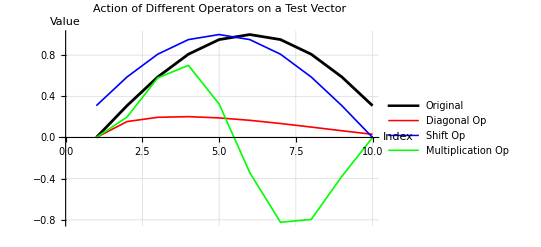
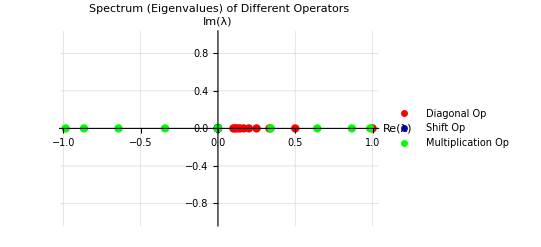

```mathematica
(* Visualize the action of these operators on a vector *)
testVector = Table[Sin[i*Pi/n], {i, 0, n-1}];

actionD1 = D1.testVector;
actionS1 = S1.testVector;
actionM1 = M1.testVector;

operatorActionPlot = ListPlot[{testVector, actionD1, actionS1, actionM1}, 
  Joined -> True,
  PlotStyle -> {{Black, Thickness[0.005]}, {Red, Thickness[0.003]}, 
               {Blue, Thickness[0.003]}, {Green, Thickness[0.003]}},
  PlotLegends -> {"Original", "Diagonal Op", "Shift Op", "Multiplication Op"},
  PlotLabel -> "Action of Different Operators on a Test Vector",
  AxesLabel -> {"Index", "Value"},
  GridLines -> Automatic];

(* Visualize the spectrum (eigenvalues) of these operators *)
eigenD1 = Eigenvalues[D1];
eigenS1 = Eigenvalues[S1];
eigenM1 = Eigenvalues[M1];

spectrumPlot = ListPlot[{
  ReIm /@ eigenD1,
  ReIm /@ eigenS1,
  ReIm /@ eigenM1
  },
  PlotStyle -> {{Red, PointSize[0.015]}, {Blue, PointSize[0.015]}, 
               {Green, PointSize[0.015]}},
  PlotLegends -> {"Diagonal Op", "Shift Op", "Multiplication Op"},
  PlotLabel -> "Spectrum (Eigenvalues) of Different Operators",
  AxesLabel -> {"Re(λ)", "Im(λ)"},
  GridLines -> Automatic,
  PlotRange -> All];

Grid[{{operatorActionPlot}, {spectrumPlot}}]
```

## Unbounded Operators

Unbounded operators are crucial in quantum mechanics and differential equations but bring additional complexity as well. An operator  is unbounded if it is not bounded, meaning for any constant : . They are not continuous and are only defined on a dense subset of the Hilbert space. Common examples are the differentiation and some integration operators.

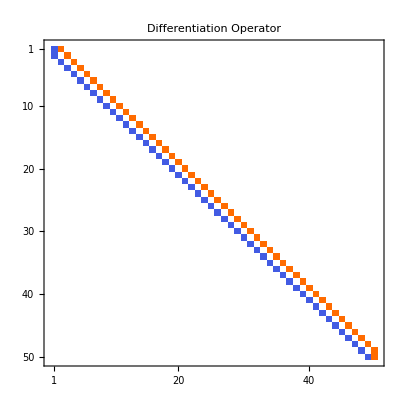

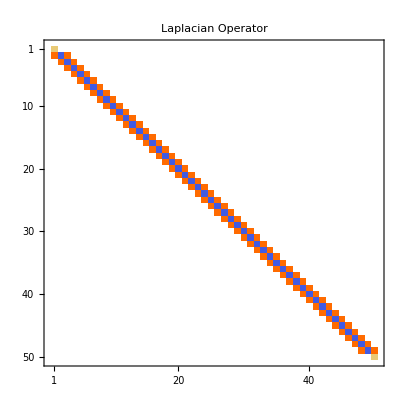

Approximate derivative of Sin(2πx) and exact result:{49 Sin[(2 π)/49],49 Sin[(4 π)/49],-49 Sin[(2 π)/49]+49 Sin[(6 π)/49],-49 Sin[(4 π)/49]+49 Sin[(8 π)/49],-49 Sin[(6 π)/49]+49 Sin[(10 π)/49],-49 Sin[(8 π)/49]+49 Sin[(12 π)/49],49 Cos[(3 π)/14]-49 Sin[(10 π)/49],49 Cos[(17 π)/98]-49 Sin[(12 π)/49],49 Cos[(13 π)/98]-49 Cos[(3 π)/14],49 Cos[(9 π)/98]-49 Cos[(17 π)/98],49 Cos[(5 π)/98]-49 Cos[(13 π)/98],49 Cos[π/98]-49 Cos[(9 π)/98],49 Cos[(3 π)/98]-49 Cos[(5 π)/98],-49 Cos[π/98]+49 Cos[π/14],-49 Cos[(3 π)/98]+49 Cos[(11 π)/98],-49 Cos[π/14]+49 Cos[(15 π)/98],-49 Cos[(11 π)/98]+49 Cos[(19 π)/98],-49 Cos[(15 π)/98]+49 Cos[(23 π)/98],-49 Cos[(19 π)/98]+49 Sin[(11 π)/49],-49 Cos[(23 π)/98]+49 Sin[(9 π)/49],49 Sin[π/7]-49 Sin[(11 π)/49],49 Sin[(5 π)/49]-49 Sin[(9 π)/49],49 Sin[(3 π)/49]-49 Sin[π/7],49 Sin[π/49]-49 Sin[(5 π)/49],-49 Sin[π/49]-49 Sin[(3 π)/49],-49 Sin[π/49]-49 Sin[(3 π)/49],49 Sin[π/49]-49 Sin[(5 π)/49],49 Sin[(3 π)/49]-49 Sin[π/7],49 Sin[(5 π)/49]-49 Sin[(9 π)/49],49 Sin[π/7]-49 Sin[(11 π)/49],-49 Cos[(23 π)/98]+49 Sin[(9 π)/49],-49 Cos[(19 π)/98]+49 Sin[(11 π)/49],-49 Cos[(15 π)/98]+49 Cos[(23 π)/98],-49 Cos[(11 π)/98]+49 Cos[(19 π)/98],-49 Cos[π/14]+49 Cos[(15 π)/98],-49 Cos[(3 π)/98]+49 Cos[(11 π)/98],-49 Cos[π/98]+49 Cos[π/14],49 Cos[(3 π)/98]-49 Cos[(5 π)/98],49 Cos[π/98]-49 Cos[(9 π)/98],49 Cos[(5 π)/98]-49 Cos[(13 π)/98],49 Cos[(9 π)/98]-49 Cos[(17 π)/98],49 Cos[(13 π)/98]-49 Cos[(3 π)/14],49 Cos[(17 π)/98]-49 Sin[(12 π)/49],49 Cos[(3 π)/14]-49 Sin[(10 π)/49],-49 Sin[(8 π)/49]+49 Sin[(12 π)/49],-49 Sin[(6 π)/49]+49 Sin[(10 π)/49],-49 Sin[(4 π)/49]+49 Sin[(8 π)/49],-49 Sin[(2 π)/49]+49 Sin[(6 π)/49],49 Sin[(4 π)/49],49 Sin[(2 π)/49]}{2 π,2 π Cos[(2 π)/49],2 π Cos[(4 π)/49],2 π Cos[(6 π)/49],2 π Cos[(8 π)/49],2 π Cos[(10 π)/49],2 π Cos[(12 π)/49],2 π Sin[(3 π)/14],2 π Sin[(17 π)/98],2 π Sin[(13 π)/98],2 π Sin[(9 π)/98],2 π Sin[(5 π)/98],2 π Sin[π/98],-2 π Sin[(3 π)/98],-2 π Sin[π/14],-2 π Sin[(11 π)/98],-2 π Sin[(15 π)/98],-2 π Sin[(19 π)/98],-2 π Sin[(23 π)/98],-2 π Cos[(11 π)/49],-2 π Cos[(9 π)/49],-2 π Cos[π/7],-2 π Cos[(5 π)/49],-2 π Cos[(3 π)/49],-2 π Cos[π/49],-2 π Cos[π/49],-2 π Cos[(3 π)/49],-2 π Cos[(5 π)/49],-2 π Cos[π/7],-2 π Cos[(9 π)/49],-2 π Cos[(11 π)/49],-2 π Sin[(23 π)/98],-2 π Sin[(19 π)/98],-2 π Sin[(15 π)/98],-2 π Sin[(11 π)/98],-2 π Sin[π/14],-2 π Sin[(3 π)/98],2 π Sin[π/98],2 π Sin[(5 π)/98],2 π Sin[(9 π)/98],2 π Sin[(13 π)/98],2 π Sin[(17 π)/98],2 π Sin[(3 π)/14],2 π Cos[(12 π)/49],2 π Cos[(10 π)/49],2 π Cos[(8 π)/49],2 π Cos[(6 π)/49],2 π Cos[(4 π)/49],2 π Cos[(2 π)/49],2 π}

Approximate derivative of Gaussian and exact result:{0.890109,1.92743,2.23393,2.56266,2.90915,3.26738,3.62978,3.98734,4.3297,4.64544,4.9224,5.14812,5.31035,5.39762,5.39979,5.30869,5.11859,4.82674,4.43362,3.94324,3.36311,2.70413,1.98026,1.20806,0.406045,-0.406045,-1.20806,-1.98026,-2.70413,-3.36311,-3.94324,-4.43362,-4.82674,-5.11859,-5.30869,-5.39979,-5.39762,-5.31035,-5.14812,-4.9224,-4.64544,-4.3297,-3.98734,-3.62978,-3.26738,-2.90915,-2.56266,-2.23393,-1.92743,-0.890109}{0.82085,0.961586,1.11509,1.27983,1.45357,1.63331,1.81527,1.99492,2.16706,2.32595,2.46547,2.57936,2.66145,2.70593,2.70771,2.66264,2.56783,2.42186,2.22498,1.97916,1.68818,1.35751,0.994189,0.606534,0.203869,-0.203869,-0.606534,-0.994189,-1.35751,-1.68818,-1.97916,-2.22498,-2.42186,-2.56783,-2.66264,-2.70771,-2.70593,-2.66145,-2.57936,-2.46547,-2.32595,-2.16706,-1.99492,-1.81527,-1.63331,-1.45357,-1.27983,-1.11509,-0.961586,-0.82085}

Approximate laplacian of Sin(2πx) and exact result:{0,-4802 Sin[(2 π)/49]+2401 Sin[(4 π)/49],2401 Sin[(2 π)/49]-4802 Sin[(4 π)/49]+2401 Sin[(6 π)/49],2401 Sin[(4 π)/49]-4802 Sin[(6 π)/49]+2401 Sin[(8 π)/49],2401 Sin[(6 π)/49]-4802 Sin[(8 π)/49]+2401 Sin[(10 π)/49],2401 Sin[(8 π)/49]-4802 Sin[(10 π)/49]+2401 Sin[(12 π)/49],2401 Cos[(3 π)/14]+2401 Sin[(10 π)/49]-4802 Sin[(12 π)/49],2401 Cos[(17 π)/98]-4802 Cos[(3 π)/14]+2401 Sin[(12 π)/49],2401 Cos[(13 π)/98]-4802 Cos[(17 π)/98]+2401 Cos[(3 π)/14],2401 Cos[(9 π)/98]-4802 Cos[(13 π)/98]+2401 Cos[(17 π)/98],2401 Cos[(5 π)/98]-4802 Cos[(9 π)/98]+2401 Cos[(13 π)/98],2401 Cos[π/98]-4802 Cos[(5 π)/98]+2401 Cos[(9 π)/98],-4802 Cos[π/98]+2401 Cos[(3 π)/98]+2401 Cos[(5 π)/98],2401 Cos[π/98]-4802 Cos[(3 π)/98]+2401 Cos[π/14],2401 Cos[(3 π)/98]-4802 Cos[π/14]+2401 Cos[(11 π)/98],2401 Cos[π/14]-4802 Cos[(11 π)/98]+2401 Cos[(15 π)/98],2401 Cos[(11 π)/98]-4802 Cos[(15 π)/98]+2401 Cos[(19 π)/98],2401 Cos[(15 π)/98]-4802 Cos[(19 π)/98]+2401 Cos[(23 π)/98],2401 Cos[(19 π)/98]-4802 Cos[(23 π)/98]+2401 Sin[(11 π)/49],2401 Cos[(23 π)/98]+2401 Sin[(9 π)/49]-4802 Sin[(11 π)/49],2401 Sin[π/7]-4802 Sin[(9 π)/49]+2401 Sin[(11 π)/49],2401 Sin[(5 π)/49]-4802 Sin[π/7]+2401 Sin[(9 π)/49],2401 Sin[(3 π)/49]-4802 Sin[(5 π)/49]+2401 Sin[π/7],2401 Sin[π/49]-4802 Sin[(3 π)/49]+2401 Sin[(5 π)/49],-7203 Sin[π/49]+2401 Sin[(3 π)/49],7203 Sin[π/49]-2401 Sin[(3 π)/49],-2401 Sin[π/49]+4802 Sin[(3 π)/49]-2401 Sin[(5 π)/49],-2401 Sin[(3 π)/49]+4802 Sin[(5 π)/49]-2401 Sin[π/7],-2401 Sin[(5 π)/49]+4802 Sin[π/7]-2401 Sin[(9 π)/49],-2401 Sin[π/7]+4802 Sin[(9 π)/49]-2401 Sin[(11 π)/49],-2401 Cos[(23 π)/98]-2401 Sin[(9 π)/49]+4802 Sin[(11 π)/49],-2401 Cos[(19 π)/98]+4802 Cos[(23 π)/98]-2401 Sin[(11 π)/49],-2401 Cos[(15 π)/98]+4802 Cos[(19 π)/98]-2401 Cos[(23 π)/98],-2401 Cos[(11 π)/98]+4802 Cos[(15 π)/98]-2401 Cos[(19 π)/98],-2401 Cos[π/14]+4802 Cos[(11 π)/98]-2401 Cos[(15 π)/98],-2401 Cos[(3 π)/98]+4802 Cos[π/14]-2401 Cos[(11 π)/98],-2401 Cos[π/98]+4802 Cos[(3 π)/98]-2401 Cos[π/14],4802 Cos[π/98]-2401 Cos[(3 π)/98]-2401 Cos[(5 π)/98],-2401 Cos[π/98]+4802 Cos[(5 π)/98]-2401 Cos[(9 π)/98],-2401 Cos[(5 π)/98]+4802 Cos[(9 π)/98]-2401 Cos[(13 π)/98],-2401 Cos[(9 π)/98]+4802 Cos[(13 π)/98]-2401 Cos[(17 π)/98],-2401 Cos[(13 π)/98]+4802 Cos[(17 π)/98]-2401 Cos[(3 π)/14],-2401 Cos[(17 π)/98]+4802 Cos[(3 π)/14]-2401 Sin[(12 π)/49],-2401 Cos[(3 π)/14]-2401 Sin[(10 π)/49]+4802 Sin[(12 π)/49],-2401 Sin[(8 π)/49]+4802 Sin[(10 π)/49]-2401 Sin[(12 π)/49],-2401 Sin[(6 π)/49]+4802 Sin[(8 π)/49]-2401 Sin[(10 π)/49],-2401 Sin[(4 π)/49]+4802 Sin[(6 π)/49]-2401 Sin[(8 π)/49],-2401 Sin[(2 π)/49]+4802 Sin[(4 π)/49]-2401 Sin[(6 π)/49],4802 Sin[(2 π)/49]-2401 Sin[(4 π)/49],0}{0,-4 π^2 Sin[(2 π)/49],-4 π^2 Sin[(4 π)/49],-4 π^2 Sin[(6 π)/49],-4 π^2 Sin[(8 π)/49],-4 π^2 Sin[(10 π)/49],-4 π^2 Sin[(12 π)/49],-4 π^2 Cos[(3 π)/14],-4 π^2 Cos[(17 π)/98],-4 π^2 Cos[(13 π)/98],-4 π^2 Cos[(9 π)/98],-4 π^2 Cos[(5 π)/98],-4 π^2 Cos[π/98],-4 π^2 Cos[(3 π)/98],-4 π^2 Cos[π/14],-4 π^2 Cos[(11 π)/98],-4 π^2 Cos[(15 π)/98],-4 π^2 Cos[(19 π)/98],-4 π^2 Cos[(23 π)/98],-4 π^2 Sin[(11 π)/49],-4 π^2 Sin[(9 π)/49],-4 π^2 Sin[π/7],-4 π^2 Sin[(5 π)/49],-4 π^2 Sin[(3 π)/49],-4 π^2 Sin[π/49],4 π^2 Sin[π/49],4 π^2 Sin[(3 π)/49],4 π^2 Sin[(5 π)/49],4 π^2 Sin[π/7],4 π^2 Sin[(9 π)/49],4 π^2 Sin[(11 π)/49],4 π^2 Cos[(23 π)/98],4 π^2 Cos[(19 π)/98],4 π^2 Cos[(15 π)/98],4 π^2 Cos[(11 π)/98],4 π^2 Cos[π/14],4 π^2 Cos[(3 π)/98],4 π^2 Cos[π/98],4 π^2 Cos[(5 π)/98],4 π^2 Cos[(9 π)/98],4 π^2 Cos[(13 π)/98],4 π^2 Cos[(17 π)/98],4 π^2 Cos[(3 π)/14],4 π^2 Sin[(12 π)/49],4 π^2 Sin[(10 π)/49],4 π^2 Sin[(8 π)/49],4 π^2 Sin[(6 π)/49],4 π^2 Sin[(4 π)/49],4 π^2 Sin[(2 π)/49],0}

Approximate laplacian of Gaussian and exact result:{0.082085,7.21357,7.80455,8.30364,8.67429,8.87862,8.8792,8.64118,8.13458,7.33668,6.23433,4.82601,3.12342,1.15255,-1.04609,-3.41808,-5.89653,-8.40448,-10.8581,-13.1705,-15.2559,-17.0343,-18.4353,-19.4024,-19.8962,-19.8962,-19.4024,-18.4353,-17.0343,-15.2559,-13.1705,-10.8581,-8.40448,-5.89653,-3.41808,-1.04609,1.15255,3.12342,4.82601,6.23433,7.33668,8.13458,8.64118,8.8792,8.87862,8.67429,8.30364,7.80455,7.21357,0.082085}{6.5668,7.21837,7.81217,8.31432,8.68815,8.89562,8.89914,8.66364,8.15896,7.36218,6.25998,4.85069,3.14594,1.17169,-1.03151,-3.4091,-5.89399,-8.40898,-10.8699,-13.1895,-15.2816,-17.0659,-18.4716,-19.4421,-19.9376,-19.9376,-19.4421,-18.4716,-17.0659,-15.2816,-13.1895,-10.8699,-8.40898,-5.89399,-3.4091,-1.03151,1.17169,3.14594,4.85069,6.25998,7.36218,8.15896,8.66364,8.89914,8.89562,8.68815,8.31432,7.81217,7.21837,6.5668}

{{Null},{Null}}

```mathematica
(*Implement a finite-dimensional approximation of the differentiation operator*)differentiationOperator[n_Integer,domainLength_:1]:=Module[{h=domainLength/(n-1),mat},mat=SparseArray[{{i_,i_}->0,{i_,j_}/;j==i+1->1/h,{i_,j_}/;j==i-1->-1/h},{n,n}];
mat[[1,1]]=-1/h;(*Forward difference at boundary*)mat[[1,2]]=1/h;
mat[[n,n-1]]=-1/h;(*Backward difference at boundary*)mat[[n,n]]=1/h;
mat]

(*Second derivative operator*)
laplacianOperator[n_Integer,domainLength_:1]:=Module[{h=domainLength/(n-1),mat},mat=SparseArray[{{i_,i_}->-2/h^2,{i_,j_}/;j==i+1->1/h^2,{i_,j_}/;j==i-1->1/h^2},{n,n}];
(*Adjust boundary conditions for Dirichlet*)mat[[1,1]]=1;(*u(0)=0*)mat[[1,2]]=0;
mat[[n,n-1]]=0;
mat[[n,n]]=1;(*u(1)=0*)mat]

(*Example usage*)
n=50;
dop=differentiationOperator[n];
lop=laplacianOperator[n];

(*Visualize the operators*)
MatrixPlot[dop,PlotLabel->"Differentiation Operator"]
MatrixPlot[lop,PlotLabel->"Laplacian Operator"]

(*Test functions*)
x=Range[0,1,1/(n-1)];
f1=Sin[2 Pi x];  (*Sin(2πx)*)
f2=Exp[-10 (x-0.5)^2];  (*Gaussian peak*)

(*Apply operators*)
Df1=dop.f1;  (*Approximate derivative of sin(2πx)*)
Df2=dop.f2;  (*Approximate derivative of Gaussian*)
Lf1=lop.f1;  (*Approximate Laplacian of sin(2πx)*)
Lf2=lop.f2;  (*Approximate Laplacian of Gaussian*)

(*Expected analytical results*)
exactDf1=2 Pi Cos[2 Pi x];
exactDf2=-20 (x-0.5) Exp[-10 (x-0.5)^2];
exactLf1=-4 Pi^2 Sin[2 Pi x];
exactLf2=(400 (x-0.5)^2-20) Exp[-10 (x-0.5)^2];

Print["Approximate derivative of Sin(2πx) and exact result:", Df1, exactDf1];
Print["Approximate derivative of Gaussian and exact result:", Df2, exactDf2];
{{Print["Approximate laplacian of Sin(2πx) and exact result:", Lf1, exactLf1];}, {Print["Approximate laplacian of Gaussian and exact result:", Lf2, exactLf2];}}
```

### Visualization

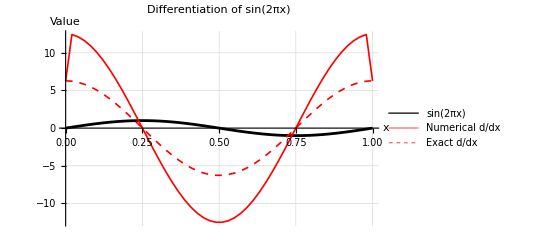
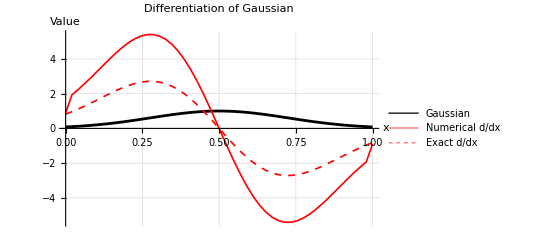
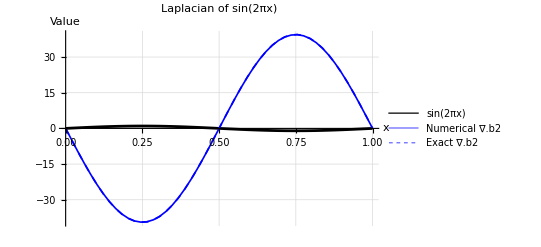
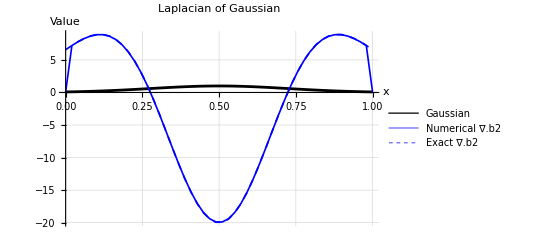
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(* Visualize the functions and their derivatives *)
derivativePlot1 = ListPlot[{
  Transpose[{x, f1}], 
  Transpose[{x, Df1}], 
  Transpose[{x, exactDf1}]
  }, 
  Joined -> True,
  PlotStyle -> {{Black, Thickness[0.005]}, {Red, Thickness[0.003]}, 
               {Red, Dashed, Thickness[0.003]}},
  PlotLegends -> {"sin(2πx)", "Numerical d/dx", "Exact d/dx"},
  PlotLabel -> "Differentiation of sin(2πx)",
  AxesLabel -> {"x", "Value"},
  GridLines -> Automatic];

derivativePlot2 = ListPlot[{
  Transpose[{x, f2}], 
  Transpose[{x, Df2}], 
  Transpose[{x, exactDf2}]
  }, 
  Joined -> True,
  PlotStyle -> {{Black, Thickness[0.005]}, {Red, Thickness[0.003]}, 
               {Red, Dashed, Thickness[0.003]}},
  PlotLegends -> {"Gaussian", "Numerical d/dx", "Exact d/dx"},
  PlotLabel -> "Differentiation of Gaussian",
  AxesLabel -> {"x", "Value"},
  GridLines -> Automatic];

laplacianPlot1 = ListPlot[{
  Transpose[{x, f1}], 
  Transpose[{x, Lf1}], 
  Transpose[{x, exactLf1}]
  }, 
  Joined -> True,
  PlotStyle -> {{Black, Thickness[0.005]}, {Blue, Thickness[0.003]}, 
               {Blue, Dashed, Thickness[0.003]}},
  PlotLegends -> {"sin(2πx)", "Numerical ∇.b2", "Exact ∇.b2"},
  PlotLabel -> "Laplacian of sin(2πx)",
  AxesLabel -> {"x", "Value"},
  GridLines -> Automatic];

laplacianPlot2 = ListPlot[{
  Transpose[{x, f2}], 
  Transpose[{x, Lf2}], 
  Transpose[{x, exactLf2}]
  }, 
  Joined -> True,
  PlotStyle -> {{Black, Thickness[0.005]}, {Blue, Thickness[0.003]}, 
               {Blue, Dashed, Thickness[0.003]}},
  PlotLegends -> {"Gaussian", "Numerical ∇.b2", "Exact ∇.b2"},
  PlotLabel -> "Laplacian of Gaussian",
  AxesLabel -> {"x", "Value"},
  GridLines -> Automatic];

Grid[{{derivativePlot1, derivativePlot2}, {laplacianPlot1, laplacianPlot2}}]
```

## Conclusion

This notebook served its purpose if you have a basic knowledge of the real-world cases that might happen with large data, or more complex problems. I hope you find it useful, and I spent a large amount of the time making sure that each topic contains a subsection for visualization. The next notebook (which is official) starts off with Quantum Mechanics, its foundations, differences with respect to Classical Mechanics, and some historical calculations.

## Further Contents

Most of the contents here are gathered again from the previous references that I have in the last notebook so I don’t mention them here